# Free undamped linear oscillations of a sagging cable and a discrete chain

It’s a story of differentiation and first-order approximations - again, and again, and again...

Rauan Kaldybayev

The work uses Newton’s second law to analyze small oscillations of a catenary cable. Rigidity, air resistance, friction, and stretching or compression due to axial stress are neglected. The aim was to compare the oscillations of a catenary cable to those of a tight straight string. It was expected to find dispersion and nonlocality, and these effects were indeed observed. One unexpected finding was that the partial differential equation governing in-plane oscillations is of fourth-order and includes mixed space and position derivatives. The work also studies the oscillations of a hanging discrete chain; it was found that a chain with a large number of elements oscillates like a continuous cable.
	To check the correctness of the work, the predicted natural frequencies were compared to those given by John Gregg Gale in his 1976 master’s thesis. The results matched, suggesting that the current computational essay is most likely correct.
	The work is useful primarily from the theoretical standpoint to better understand the physics of oscillations, as the systems explored here exhibit exotic behaviors like nonlocality. Empirical observations made here lead to a general conjecture regarding oscillatory systems, namely the existence of “natural coordinates” (explained later in the abstract). The essay can also be used to estimate the frequencies of conductor galloping, which is a major question in engineering.
	The first novelty of this essay is that it uses a unique approach that is based on curvilinear coordinates, as opposed to past works, which used a more visual approach. The present work is more formal: it starts with Newton’s second law and the incompressibility condition and transforms the equations in various ways using geometrical identities. The equations of motion yielded by this method are written in terms of the cable’s perpendicular displacement only, as opposed to other works, which also used quantities like angles. This can make the physical meaning of the equations more transparent.
	The two PDEs have variable coefficients and include second-order time derivatives. The first equation describes horizontal oscillations and includes second-order position derivatives. The second equation describes in-plane oscillations and involves fourth-order position derivatives and mixed derivatives. The PDEs are independent.
	Arc length, displacement of the cable from equilibrium, and Cartesian coordinates are the most intuitive coordinates for the problem. Turns out, they also have convenient mathematical properties. The normal modes of horizontal oscillations are orthogonal when arc length is used as the spatial coordinate. The equations of motion of the cable are independent when written in terms of the cable’s horizontal and in-plane displacement from equilibrium. The PDEs describing the cable’s oscillations have polynomial coefficients when the vertical coordinate z is used as the spatial coordinate. The PDE describing the normal mods of horizontal oscillations takes the simple form ψ''[χ] + ϖ^2 Cosh[χ] ψ[χ] = 0 when the horizontal coordinate x is used as the spatial coordinate. Maybe in general, every system has its own “natural coordinates”, which are most convenient when studying the system and can be guessed from physical intuition?
	Having derived the equations of motion, the work explores their behavior in the limiting cases, when the cable is hung very tightly (e.g. its ends are pulled far from each other and the cable straightens out) and when the cable has a large sag (e.g. when its endpoints are brought together, almost touching each other). While the equations are generally complicated and couldn’t be solved analytically, their behavior in these limiting cases is comparatively simple. For a lax cable, the normal modes can be expressed through Bessel functions. For a tight cable, an approximate algebraic formula for the natural frequencies and normal modes is given. The formula is quick to compute numerically but can be difficult to analyze due to the presence of hypergeometric functions. Saxon and Cahn’s 1953 article gives a different estimate for the natural frequencies.
	Empirically, it was observed that the normal modes have greater curvature and amplitude near the cable’s lowest point, and near the edges, they flatten out and decrease in amplitude. This is because tension is lowest at the bottom of the cable and increases from there.
	The equations of horizontal and in-plane oscillations of a sagging discrete chain are, respectively, d^2/dt^2 θ = -Y θ, d^2/dt^2 φ = - K φ, where θ and φ are vectors of dimension N and N - 1, respectively, for N ∈ Z^+, and Y and K are square matrices of corresponding dimensions. It was empirically observed that a chain with a large number of elements oscillates like a continuous cable – it has the same natural frequencies and normal modes, and the eigenvalues of the matrices Y and K converge to certain limits.
	In addition, the essay features many visualizations and illustrations (including interactive animations), which make the content more intuitive. It also includes Wolfram Language code, which can often give a clearer picture, for example, when illustrating a numerical method.
	To study the oscillations of a catenary cable, the essay starts by finding the cable’s equilibrium configuration; in addition to mathematical formulas, it presents Wolfram Language functions to automatically compute the cable’s shape. Curvilinear coordinates fitted to the cable’s equilibrium shape are defined. Two PDEs describing the cable’s small oscillations are derived from Newton’s second law, incompressibility condition, and geometrical identities. The PDEs are non-dimensionalized and solved as a superposition of their normal modes. The normal modes could not be found analytically, so an approach based on Frobenius’s method was used. The solution was calculated automatically using frobeniusDSolve, a Wolfram Language function was written as a part of the project. The function has many possible applications in other problems.
	To study the oscillations of a discrete chain, Newton’s second law is first written, and the equilibrium is found; Wolfram Language functions are presented alongside mathematical formulas. Newton’s 2nd law is linearized to explore small oscillations. Using boundary conditions, two independent ODEs of motion are then obtained: d^2/dt^2 θ = -Y θ, d^2/dt^2 φ = - K φ, where θ and φ are vectors and Y and K are square matrices. Natural frequencies and normal modes are computed through the eigenvalues and eigenvectors of these matrices. Empirically it is observed that the normal modes and natural frequencies of a discrete chain with a large number of elements are the same as those of a continuous cable.

## Introduction

## Why is this interesting?

The original motivation for this work came from the YouTube video where a stay cable was hit with a wrench and produced awesome Star Wars blaster sounds. I looked up some articles on this topic and was immediately fascinated - not by the sound, however, but by the oscillations themselves.
	A vibrating string - a classic example of an oscillatory system. The system is governed by the wave equations (∂^2 y)/(∂t^2) = (∂^2 y)/(∂x^2), the normal modes of which are sine functions, and the dispersion relation is linear - simple. If we have two strings with different densities are connected to each other, things get more interesting. A pulse travelling from one string to another would partially reflect at the sewing point because of impedance mismatch. Things are even more interesting when a string is hung vertically and impedance changes continuously. The normal modes are then written through Bessel functions, and dispersion appears. We can see that from a simple string, we can get a wide range of fascinating behaviors.
	But what if we go a bit further and hang the string from two points that are not on the same vertical, such that the string would be sagging? How would the string oscillate then? There are many effects we would expect: dispersion due to variable tension, pulses “continuously reflecting” when travelling because of changing tension. We might even expect nonlocality - if we pick such a string at one point, the entire string will have to move immediately because otherwise its length would change. As for the normal modes of this system, even trying to imagine them is difficult.
	The problem discussed in here is interesting first of all from the theoretical standpoint. It can be curious to people interested in the physics of oscillations and to students learning about the topic. As mentioned above, the system features interesting phenomena like dispersion, “continuous reflection”, and nonlocality; in addition, as will be shown below, one of the PDEs describing the cable’s oscillations actually contains fourth-order position derivatives and mixed position and time derivatives, which is quite exotic for Newtonian mechanics. The results reached in this work can also be applied on practice to estimate the normal frequencies of conductor galloping, which is a very relevant issue in engineering. There exist more accurate models of conductor galloping, however, the model presented here is particularly simple because it’s linear; the theory can be helpful as a first introduction.

## Cable in equilibrium; Cartesian coordinates

A cable is hung between two fixed points - let’s call them O and P. The force of gravity pulls the cable down, while the force of tension keeps it in place. In equilibrium, the cable takes the shape that minimizes its potential energy. This shape is known as catenary:

-Graphics3D-

To describe the system, we can use Cartesian coordinates where the point O is the origin of coordinates, the z axis goes vertically upward (against the force of gravity), and the x axis goes horizontally such that the points O and P lie in the x-z plane. In these coordinates, the equilibrium shape of the cable is given by the function z_e[x] (see derivation in the uncut version):

z_e[x] = Λ (Cosh[(x - x_0)/Λ] - Cosh[x_0/Λ])

Here Λ and x_0 are constants determined from the boundary conditions, e.g. are picked such that the curve would pass through the points O and P. The subscript e in z_e[x] denotes that the function describes the cable’s equilibrium. In equilibrium, the cable lies in the x-z plane, so

y_e[x] = 0

The meaning of the functions y_e[x] and z_e[x] is that if we pick some point on the cable when it’s in equilibrium, then the coordinates x, y, z of this point would be related by (1) and (2). When the cable is displaced from equilibrium, its shape would of course be different, and the functions y[x] and z[x] describing its new shape would be different from y_e[x] and z_e[x].

#### Code used to generate the figure

```mathematica
With[{xp = 3, Λ = 1, x0 = 1}, Labeled[
	Show[{
		ParametricPlot3D[
			{x, 0, Λ(Cosh[(x - x0)/Λ] - Cosh[x0/Λ])},
			{x, 0, xp},
			PlotStyle -> {Darker@Green, Thick}, PlotRange->{Automatic, {-1.4, 1.4},  Automatic}
		],
		Graphics3D[{
			{Arrow[{{0, 0, 0}, {0.7, 0, 0}}]}, {Text[Style["X", Bold, 12, FontFamily -> "Computer Modern"], {0.9, 0, 0}]},
			{Arrow[{{0, 0, 0}, {0, 0.7, 0}}]}, {Text[Style["Y", Bold, 12, FontFamily -> "Computer Modern"], {0, 0.9, 0}]},
			{Arrow[{{0, 0, 0}, {0, 0, 0.7}}]}, {Text[Style["Z", Bold, 12, FontFamily -> "Computer Modern"], {0, 0, 0.9}]},
			{Opacity[0.1], InfinitePlane[{{0, 0, 0}, {1, 0, 0}, {0, 0, 1}}]},
			{PointSize[Large], Point[{0, 0, 0}]}, {Text[Style["O", Bold, 12, FontFamily -> "Computer Modern"], {0, -0.4, 0}]},
			{PointSize[Large], Point[{xp, 0, Λ(Cosh[(xp - x0)/Λ] - Cosh[x0/Λ])}]}, {Text[Style["P", Bold, 12, FontFamily -> "Computer Modern"], {xp, -0.4, Λ(Cosh[(xp - x0)/Λ] - Cosh[x0/Λ])}]}
		}]
	}, ImageSize -> Medium, ViewPoint -> {2.1, -2.7, 0.9}],
	LineLegend[{Darker@Green}, {"Cable in equilibrium"}]
]]
```

## Assumptions

This work neglects friction and air resistance, the cable’s stiffness, and stretching and compression due to axial stresses.

From physical intuition, we can guess that air resistance is negligible for massive cables. A small grain of dust is easily dragged by slightest movements of air, while a large boulder can only be moved by powerful storms. The stiffness of the cable can also be neglected for large cables. When Titanic capsized and its bow rose into the air, the ship broke in half under its own weight; the force of gravity dominated the structure’s strength. On the other hand, a smaller model of the same ship can easily support itself; elastic forces are much stronger than the force of gravity. This shows that the larger the object, the more is the degree to which gravity dominates elastic forces. Again, for sufficiently large cables, we can neglect stiffness altogether.

-Graphics--Graphics-

On the left, you see an illustration of Titanic breaking in half due to the mechanical stresses (taken from https://www.britannica.com/story/timeline-of-the-titanics-final-hours). On the right is shown a smaller model of Titanic; the model can easily support its weight even though it sits on a narrow base.

The third assumption is that we can neglect compression and stretching due to axial stresses. To see that this approximation is valid, let us use Hooke’s law, which states that the relative elongation of a small piece of cable is given by ε = σ/E, where σ is stress and E is the Young modulus of the cable’s material, say steel. To estimate the order of magnitude of σ, we can use dimensional analysis, which yields that σ ~ ρ g L, where ρ is the density of steel, g is the free fall acceleration, and L is the cable’s length. For ε, we then have ε ~ (ρ g L)/E. If we want ε to be less than 10^-3, L must be smaller than approximately 2500 meters (with ρ = 8000, g = 10, E = 2 · 10^11, all in SI units). The approximation holds for cables under 2500 meters in length, or basically for all cables we would normally see.

### Small oscillations

The current work investigates small oscillations, when the displacement from equilibrium is very small. Mathematically, we describe the cable’s shape using some set of variables, or generalized coordinates. For each generalized coordinate q, we have

q = q_e + O[ε]

where q stands for some (or any) generalized coordinate, q_e is the value of q in equilibrium, and ε is a small number. The current work assumes that for each generalized coordinate, there is exactly one equilibrium value; there is only one equilibrium configuration for a cable hung between two points, so it only makes sense if the generalized coordinates describing it also have only one equilibrium value. For a generic system, of course, there might be multiple equilibrium configurations, and (3) would not be true.
	For small oscillations, ε << 1. This means that in an expression of the form a_0 + a_1 ε + a_2 ε^2 + ... + a_n ε^n, we may only leave the first few terms, as all the following terms would be negligibly small. Most of the times, we would only leave the a_0 term.

## Curvilinear coordinates

## Definition

When studying small oscillations of a given system, it is convenient to choose coordinates that are somehow fitted to the system’s equilibrium. When studying a mathematical pendulum, we usually use the angle φ between the rod and the vertical as the coordinate. This choice is convenient because we then have φ = 0 in equilibrium. In the case of a hanging cable, we can try and pull off a similar trick, namely to use the cable’s displacement from equilibrium as our coordinates.
	We can do that with the help of curvilinear coordinates fitted to the cable’s equilibrium shape. In exactly the same way we parametrized the cable in Cartesian coordinates as y = y[x], z = z[x], we can parametrize it in any other coordinate system. Instead of x, let us use ζ, and let us also change z to h, so that the cable’s shape is now parametrized as y = y[ζ], h = h[ζ], where y is the good old Cartesian y and ζ, h are curvilinear coordinates to be defined later. We want to define the coordinates ζ, h such that the cable’s equilibrium shape would correspond to y[ζ] = 0, h[ζ] = 0, in analogy to how the equilibrium position of a mathematical pendulum corresponds to φ = 0. In this case, y[ζ] and h[ζ] would actually be measuring the cable’s displacement from equilibrium. We already have y_e = 0 (2), so there is no need to replace the coordinate y. Now that we know what we are looking for, let us move on to actually defining ζ and h.

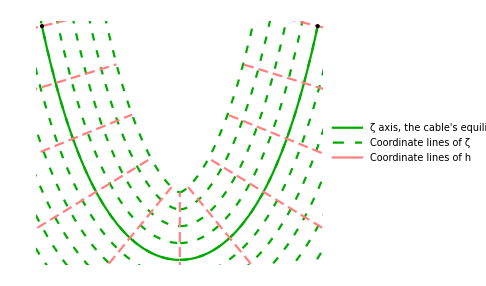

Let’s first look at the x-z plane. We know that in equilibrium, the cable takes the shape of a catenary. So, an intuitive thing to do would be to take h to be the distance from the equilibrium catenary (up to a minus sign). More formally, the coordinate h of a given point in the x-z plane is, up to a sign, the distance from that point to the equilibrium catenary. If the point is above the equilibrium catenary, then h is positive, and if the point is below, then h is negative.
	Let us name the second coordinate ζ. To determine the coordinate ζ of a given point A, find the point on the equilibrium catenary that is closest to A and call this point C. The coordinate ζ_A of the point A is defined to be the arc length along the equilibrium catenary from the point O to the point C. As you can see from the figure below, ζ_A = OC, h_A = ±AC.

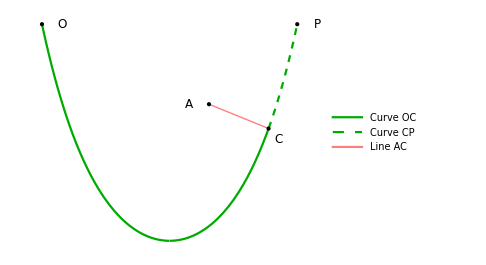

To coordinatize three-dimensional space, we need one more coordinate. Since in equilibrium the cable rests in the x-z plane, the Cartesian coordinate y already measures its displacement from equilibrium and hence is fine to use. Let us then proceed to integrating it into our ζ, h coordinate system. Given a point A, take the perpendicular from A to the x-z plane. Call the intersection of this perpendicular with the x-z plane D. We then have y_A = ±AD, h_A = ±CD, ζ_A = OC. On the figure below, the point A lies in the -y halfspace, so  y_A is negative.

-Graphics3D-

The coordinates ζ_A, y_A, h_A  of the point A tells us exactly where the point A is. Mathematically, we can write

r^– = r^–[ζ, y, h]

Where r^– is the position vector of a given point. The formula above simply says that the position of a point can be described using the coordinates ζ, y, h. The explicit transformation formula from ζ, h to x, z can be found from the formula (1) and the definitions of ζ and h.

x[ζ, h] = x_0 + Λ ArcSinh[(ζ - l_0)/Λ] - ((ζ - l_0)/Λ)/(√(1  + ((ζ - l_0) / Λ)^2)) h
z[ζ, h] = Λ (√(1 + ((ζ - l_0)/Λ)^2) - √(1 + (l_0/Λ)^2)) + 1/(√(1  + ((ζ - l_0) / Λ)^2)) h

#### Code used to generate the figures

```mathematica
ClearAll[findLambda];
findLambda[L_, xp_, zp_] := With[
	{
		D = Sqrt[L^2 - zp^2] / xp
	},
	If[(!Element[D, Reals]) || (D < 1),
		$Failed,
		(If[#[[1, 2]] > 0, xp / (2 #[[1, 2]]), Nothing]& /@ 
			NSolve[D == Sinh[ϕ] / ϕ, ϕ, Reals, WorkingPrecision -> MachinePrecision])[[1]]
	]
];
```

```mathematica
ClearAll[findX0];
findX0[L_, xp_, zp_, Λ_] := xp / 2 - Λ ArcTanh[zp / L];
```

```mathematica
Block[
	{
		L = 2, xp = 1, zp = 0,
		Λ, x0, l0,
		xe, ze, ζbar, hbar,
		ζlines, hlines, ζ, h
	},
	Λ = findLambda[L, xp, zp];
	x0 = findX0[L, xp, zp, Λ];
	l0 = Λ Sinh[x0 / Λ];

	xe = Function[ζ, x0 + Λ ArcSinh[(ζ - l0)/Λ]];
	ze = Function[ζ, Λ (√(1 + ((ζ - l0)/Λ)^2) - √(1 + (l0/Λ)^2))];
	ζbar = Function[ζ, {1, (ζ - l0)/Λ}/(√(1 + (ζ - l0)^2/Λ^2))];
	hbar = Function[ζ, {-(ζ - l0)/Λ, 1}/(√(1 + (ζ - l0)^2/Λ^2))];
	
	ζlines = Plus[# hbar[ζ], {xe[ζ], ze[ζ]}]& /@ Range[-2Λ, Λ, Λ/4];
	hlines = Plus[h hbar[#], {xe[#], ze[#]}]& /@ Range[0, L, L/10];
	
	Legended[Show[{
		ParametricPlot[{xe[ζ], ze[ζ]},
			{ζ, 0, L},
			PlotStyle -> {Thick, Darker@Green},
		Axes -> False
		],
		ParametricPlot[ζlines,
			{ζ, -L, 2L},
			PlotStyle -> Array[{Thin, Dashing[{0.015, 0.02}], Darker@Green}&, Length@ζlines]
		],
		ParametricPlot[hlines,
			{h, -2Λ, Λ},
			PlotStyle -> Array[{Thin, Dashing[{0.02, 0.01}], Pink}&, Length@ζlines]
		],
		Graphics[{
			{PointSize[Large], Point[{0, 0}]},
			{PointSize[Large], Point[{xp, zp}]}
		}]
	}, ImageSize -> Medium], LineLegend[{Darker@Green, {Dashed, Darker@Green}, Pink},
	{"ζ axis, the cable's equilibrium shape", "Coordinate lines of ζ", "Coordinate lines of h"}]]
]
```

```mathematica
Block[
	{
		L = 2, xp = 1, zp = 0,
		Λ, x0, l0,
		xe, ze, hbar,
		ζ, h,
		ζA = 1.6, hA = 0.25
	},
	Λ = findLambda[L, xp, zp];
	x0 = findX0[L, xp, zp, Λ];
	l0 = Λ Sinh[x0 / Λ];

	xe = Function[ζ, x0 + Λ ArcSinh[(ζ - l0)/Λ]];
	ze = Function[ζ, Λ (√(1 + ((ζ - l0)/Λ)^2) - √(1 + (l0/Λ)^2))];
	hbar = Function[ζ, {-(ζ - l0)/Λ, 1}/(√(1 + (ζ - l0)^2/Λ^2))];
	
	Legended[Show[{
		ParametricPlot[{xe[ζ], ze[ζ]},
			{ζ, 0, ζA},
			PlotStyle -> {Thick, Darker@Green},
			Axes -> False
		],
		ParametricPlot[{xe[ζ], ze[ζ]},
			{ζ, ζA, L},
			PlotStyle -> {Thick, Dashed, Darker@Green},
			Axes -> False
		],
		Graphics[{
			{PointSize[Large], Point[{0, 0}]},
			{PointSize[Large], Point[{xp, zp}]},
			{Thick, Pink, Line[{{xe[ζA], ze[ζA]}, {xe[ζA], ze[ζA]} + hA hbar[ζA]}]},
			{PointSize[Large], Point[{xe[ζA], ze[ζA]} + hA hbar[ζA]]}, {Text[Style["A", 12], {xe[ζA], ze[ζA]} + hA hbar[ζA] - {0.08, 0}]},
			{PointSize[Large], Point[{xe[ζA], ze[ζA]}]}, {Text[Style["C", 12], {xe[ζA], ze[ζA]} + {0.04, -0.04}]},
			{Text[Style["O", 12], {0.08, 0}]},
			{Text[Style["P", 12], {xe[L], ze[L]} + {0.08, 0}]}
		}]
	}, ImageSize -> Medium, PlotRange -> All], LineLegend[{Darker@Green, {Thick, Dashed, Darker@Green}, Pink},
	{"Curve OC", "Curve CP", "Line AC"}]]
]
```

```mathematica
Block[
	{
		L = 2, xp = 1, zp = 0,
		Λ, x0, l0,
		xe, ze, hbar,
		ζ, h,
		ζA = 1.6, yA = -0.4, hA = 0.25
	},
	Λ = findLambda[L, xp, zp];
	x0 = findX0[L, xp, zp, Λ];
	l0 = Λ Sinh[x0 / Λ];

	xe = Function[ζ, x0 + Λ ArcSinh[(ζ - l0)/Λ]];
	ze = Function[ζ, Λ (√(1 + ((ζ - l0)/Λ)^2) - √(1 + (l0/Λ)^2))];
	hbar = Function[ζ, {-(ζ - l0)/Λ, 0, 1}/(√(1 + (ζ - l0)^2/Λ^2))];
	
	Legended[Show[{
		ParametricPlot3D[{xe[ζ], 0, ze[ζ]},
			{ζ, 0, ζA},
			PlotStyle -> {Thick, Darker@Green},
			Axes -> False
		],
		ParametricPlot3D[{xe[ζ], 0, ze[ζ]},
			{ζ, ζA, L},
			PlotStyle -> {Thick, Dashed, Darker@Green},
			Axes -> False
		],
		Graphics3D[{
			{Opacity[0.1], InfinitePlane[{{0, 0, 0}, {0, 0, 1}, {1, 0, 0}}]},
			{PointSize[Large], Point[{0, 0, 0}]},
			{PointSize[Large], Point[{xp, 0, zp}]},
			{Thick, Pink, Line[{{xe[ζA], 0, ze[ζA]}, {xe[ζA], 0, ze[ζA]} + hA hbar[ζA]}]},
			{Thick, Darker@Cyan, Line[{{xe[ζA], 0, ze[ζA]} + hA hbar[ζA], {xe[ζA], yA, ze[ζA]} + hA hbar[ζA]}]},
			{PointSize[Large], Point[{xe[ζA], yA, ze[ζA]} + hA hbar[ζA]]}, {Text[Style["A", 12], {xe[ζA], yA, ze[ζA]} + hA hbar[ζA] - {0.08, 0, 0}]},
			{PointSize[Large], Point[{xe[ζA], 0, ze[ζA]} + hA hbar[ζA]]}, {Text[Style["D", 12], {xe[ζA], 0, ze[ζA]} + hA hbar[ζA] - {0.08, 0, 0}]},
			{PointSize[Large], Point[{xe[ζA], 0, ze[ζA]}]}, {Text[Style["C", 12], {xe[ζA], 0, ze[ζA]} + {0.04, 0, -0.04}]},
			{Text[Style["O", 12], {0.08, 0, 0}]},
			{Text[Style["P", 12], {xe[L], 0, ze[L]} + {0.08, 0, 0}]}
		}]
	}, ImageSize -> Medium, PlotRange -> All, ViewPoint -> {0.7, -0.4, 0.6}], LineLegend[{Darker@Green, {Thick, Dashed, Darker@Green}, Pink, Darker@Cyan},
	{"Curve OC", "Curve CP", "Line DC", "Line AD"}]]
]
```

### Using the coordinate system ζ, y, h to describe the cable’s shape

Now that we have defined the coordinates ζ and h, we can parametrize the cable’ shape as y = y[ζ], h = h[ζ]. And since the cable’s shape changes in time when it oscillates, it is actually more appropriate to write

y = y[t, ζ]
h = h[t, ζ]

What these formulas tell us is that at some instant t, if we take a point with coordinate ζ on the cable, then the coordinates y, h of this point are given by y = y[t, ζ], h = h[t, ζ].

## Geometrical identities involving the basis vectors

We have successfully defined a curvilinear coordinate system ζ, y, h. Now, to successfully use Newton’s second law, which is a vector equation, we will need to define the basis vectors and derive some useful geometrical identities.

### Basis vectors

Let us define the basis vectors ζ^̑, y^̑, h^̑ as

ζ^̑ ≡ (∂r^–)/(∂ζ)
y^̑ ≡ (∂r^–)/(∂y)
h^̑ ≡ (∂r^–)/(∂h)

where r^– = r^–[ζ, y, h] (4). The physical meaning of ζ^̑ is that if we increase the coordinate ζ of a point by some infinitesimal value dζ while leaving its coordinates y and h fixed, then the point would move by ζ^̑ dζ; the same is true of y^̑ and h^̑.
	Now, from the figure before the equation (4), we can see that the basis vectors ζ^̑, y^̑, h^̑ are orthogonal. This can be proven by “brute force” from (5) and (6), and this is in fact done below. But here is a visual explanation. Increasing y_A while leaving h_A and ζ_A fixed means increasing AD while leaving CD and OC fixed, or basically moving the point A away or towards the x-z plane; thus, y^̑ is directed along AD. Similarly, we get that h^̑ is directed along the line CD. Since AD is perpendicular to the x-z plane, we conclude that y^̑ and h^̑ are orthogonal. Increasing the coordinate ζ_A leaving y_A and h_A fixed means moving the point C further along the equilibrium catenary while holding AD and CD fixed. From here, we see that the basis vector ζ^̑ is directed along the tangent line to the equilibrium catenary at the point C. Since CD is perpendicular to the equilibrium catenary, ζ^̑ is orthogonal to h^̑; and since AD is perpendicular to the x-z plane and ζ^̑ lies in the x-z plane, we get that ζ^̑ is also orthogonal to y^̑.

ζ^̑ · y^̑ = 0
ζ^̑ · h^̑ = 0
y^̑ · h^̑ = 0

y_A is defined to be the distance from A to the x-z plane, and h_A is the distance from A to the equilibrium catenary. The coordinates y and h are distances, so (y^̑)^2 = (h^̑)^2 = 1.

y^̑ · y^̑ = 1
h^̑ · h^̑ = 1

The norm of ζ^̑ is generally a function of position, however, it equals 1 when y = h = 0, and here is why. If the coordinates y_A and h_A of the point A are both zero, then the point A lies on the equilibrium catenary. In this case, ζ, which is defined to be the length of the curve OC, is equal to the length of the curve OA. The coordinate ζ then becomes the distance from O to A along the equilibrium catenary, and increasing ζ_A by dζ is then equivalent to moving the point A by the distance dζ along the equilibrium catenary. We thus have (ζ^̑)^2 = 1 for y = h = 0.

ζ^̑ · ζ^̑ = f^2[ζ, h]
f[ζ, 0] = 1

Here f[ζ, h] is some function of ζ and h that can be found from the formula (1), which tells us the shape of the equilibrium catenary, and the definition of the curvilinear coordinates ζ, y, h. The function f does not depend on y because of translation symmetry: if f did depend on y, then the norm of ζ^̑ would also depend on y, which does not make any sense; this is proven in the subsection "Derivatives involving y".
	We can check the formulas (7),  (8), (9) using the transformation formula from ζ, h to x, z (5) and the definition of ζ^̑, y^̑, h^̑:

```mathematica
Block[{r = {
			x0 + Λ ArcSinh[(ζ - l0)/Λ] - ((ζ - l0)/Λ)/(√(1  + ((ζ - l0) / Λ)^2)) h,
			y,
			Λ (√(1 + ((ζ - l0)/Λ)^2) - √(1 + (l0/Λ)^2)) + 1/(√(1  + ((ζ - l0) / Λ)^2)) h
		},
		ζbar, ybar, hbar
	},
	ζbar = D[r, ζ];
	ybar = D[r, y];
	hbar = D[r, h];
	
	Column[{
		Row[{"ζ^̑ · y^̑ = ", Simplify@Dot[ζbar, ybar]}],
		Row[{"ζ^̑ · h^̑ = ", Simplify@Dot[ζbar, hbar]}],
		Row[{"y^̑ · h^̑ = ", Simplify@Dot[ybar, hbar]}],
		Row[{"y^̑ · y^̑ = ", Simplify@Dot[ybar, ybar]}],
		Row[{"h^̑ · h^̑ = ", Simplify@Dot[hbar, hbar]}],
		Row[{"ζ^̑ · ζ^̑ = ", Simplify@Dot[ζbar, ζbar]}],
		Row[{"(ζ^̑ · ζ^̑)_(h  =  0) = ", Simplify[Dot[ζbar, ζbar] /. h -> 0]}]
	}]
]
```

ζ^̑ · y^̑ = 0
ζ^̑ · h^̑ = 0
y^̑ · h^̑ = 0
y^̑ · y^̑ = 1
h^̑ · h^̑ = 1
ζ^̑ · ζ^̑ = ((l0^2-2 l0 ζ+ζ^2+Λ (-h+Λ))^2)/((l0^2-2 l0 ζ+ζ^2+Λ^2)^2)
(ζ^̑ · ζ^̑)_(h  =  0) = 1

### Symmetry of the derivatives of the basis vectors

From the definition of ζ^̑, y^̑, h^̑ (6) and the commutativity of partial derivatives, we have

(∂ζ^̑)/(∂h) = (∂h^̑)/(∂ζ)
(∂ζ^̑)/(∂y) = (∂y^̑)/(∂ζ)
(∂h^̑)/(∂y) = (∂y^̑)/(∂h)

### Derivatives involving y

y is a Cartesian coordinate, which means that its basis vector y^̑ is constant:

(∂y^̑)/(∂ζ) = 0
(∂y^̑)/(∂y) = 0
(∂y^̑)/(∂h) = 0

Using (10), we also get that

(∂ζ^̑)/(∂y) = 0
(∂h^̑)/(∂y) = 0

Now, let’s prove that f does not depend on y. If we treat f as f[ζ, y, h], differentiating the definition of f, which is ζ^̑ · ζ^̑ = f^2(9), with respect to y gives ζ^̑·(∂ζ^̑)/(∂y) = f(∂f)/(∂y). As we have just shown, (∂ζ^̑)/(∂y) = 0 (12). Thus, (∂f)/(∂y) = 0 as well, which means that f does not depend on y. □

### Finding (∂h^̑)/(∂ζ)

Taking the derivative of y^̑ · h^̑ = 0 (7) with respect to ζ, we get

y^̑ · (∂h^̑)/(∂ζ)  +(∂y^̑)/(∂ζ) · h^̑ = 0

Since y^̑ is constant (11), the second term is zero.

y^̑ · (∂h^̑)/(∂ζ)  = 0

This means that (∂h^̑)/(∂ζ) is orthogonal to y^̑. Differentiating h^̑ · h^̑ = 1 (8) with respect to ζ tells us that (∂h^̑)/(∂ζ) is also orthogonal to h.

h^̑ · (∂h^̑)/(∂ζ) = 0

Since (∂h^̑)/(∂ζ) is orthogonal to both y^̑ and h^̑, it can only point in the ζ direction, e.g. it must be a multiple of ζ^̑: (∂h^̑)/(∂ζ) = W[ζ, y, h] ζ^̑. At this point, we don’t know what W is. But just intuitively, W must have some relation to the curvature of the coordinate curves. And in fact, after doing the calculations, it turns out that W[ζ, y, h] = -k[ζ, h], where k[ζ, h] is the curvature of the coordinate curves of ζ (see proof here).

(∂h^̑)/(∂ζ) = -k[ζ, h] ζ^̑

The function k does not depend on y. Taking the dot product of the formula (13) with ζ^̑ and using ζ^̑ · ζ^̑ = f^2 (9), we get ζ^̑ · (∂h^̑)/(∂ζ) = -k f^2. If we now differentiate this with respect to y taking k to also be a function of y, such that k = k[ζ, y, h], we get the equation ∂/(∂y)(∂h^̑)/(∂ζ) = -(∂k)/(∂y)ζ^̑ - k (∂ζ^̑)/(∂y). Changing the order of partial derivatives on the left-hand side and using (∂ζ^̑)/(∂y) = (∂h^̑)/(∂y)  = 0 (12), we get (∂k)/(∂y) = 0, which means that indeed, k not depend on y. □
	It’s important to realize that what k in (13) tells us is not the cable’s curvature. Instead, k tells us the curvature of the coordinate lines of ζ. Although in equilibrium the cable does lie on the ζ axis, the cable’s shape is generally different.

### Other identities

By repeatedly differentiating and combining the formulas (6)-(13), the following identities can be derived. The derivation is given in the uncut version, chapter “Curvilinear coordinates”, section “Derivatives”.

(∂ζ^̑)/(∂h) = -k[ζ, h] ζ^̑

(∂h^̑)/(∂h) = 0

(∂ζ^̑)/(∂ζ) = 1/f(∂f)/(∂ζ) ζ^̑ + k f^2 h^̑

k[ζ, h]= k_e[ζ]/(1 - k_e[ζ]h)

f[ζ, h] = 1 - k_e[ζ] h

Here, k_e[ζ] ≡ k[ζ, 0] tells us the curvature of the ζ axis. By definition, the ζ axis is the cable’s equilibrium catenary. We can calculate the curvature of the latter using the formula (1). Thus, for k_e we have

k_e[ζ] ≡ k[ζ, 0] = 1/Λ 1/(1 + ((ζ - l_0)/Λ)^2)

where l_0 ≡ Λ Sinh[x_0/Λ].

### Why k is the curvature of coordinate lines of ζ

Given a curve, we can parametrize it as (r^–)_c = (r^–)_c[s]. This formula tells us the position vector (r^–)_c of a point on the curve as a function of arc length s.

(r^–)_c = (r^–)_c[s]

The curvature of this curve is then defined as

κ ≡ |(d^2(r^–)_c)/ds^2|

Let us examine the curves given by ζ = ζ[s], y = const, h = const, in other words - coordinate lines of ζ. By chain rule, (d(r^-)_c)/ds = (∂r^–)/(∂ζ)dζ_c/ds + (∂r^–)/(∂y)dy_c/ds + (∂r^–)/(∂h)dh_c/ds,

(d(r^–)_c)/ds = (∂r^–)/(∂ζ)dζ_c/ds + (∂r^–)/(∂y)dy_c/ds + (∂r^–)/(∂h)dh_c/ds

where the partial derivatives (∂r^–)/(∂ζ), (∂r^–)/(∂y), (∂r^–)/(∂h) are evaluated at the point (r^–)_c[s]. Because y_c = const, h_c = const, we have dy_c/ds = dh_c/ds = 0, and the formula becomes (d(r^–)_c)/ds = (∂r^–)/(∂ζ)dζ_c/ds. By definition, (∂r^–)/(∂ζ) ≡ ζ^̑ (6), so we have

(d(r^–)_c)/ds = (ζ^̑)_c dζ_c/ds

Here, the subscript c in (ζ^̑)_c indicates that ζ^̑[ζ, h] is evaluated at the point (r^–)_c, (ζ^̑)_c[s] ≡ ζ^̑[ζ_c[s], h_c]. Using the fact that du/dv = 1/dv/du, we can re-write this formula as

(d(r^–)_c)/ds = (ζ^̑)_c / ds/dζ_c

Here, ds/dζ tells us how much arc length we cover if we increase ζ_c by dζ. By definition, this is the norm of (ζ^̑)_c, which equals f[ζ_c[s], h_c] (9). Another way to see that is that since the unit tangent vector has norm 1 and (d(r^–)_c)/ds is precisely the unit tangent vector, then it must have norm 1. Equating the norm of (ζ^̑)_c/ds/dζ to 1 keeping in mind that the norm of ζ^̑ is by definition f (9), we get that ds/dζ_c = f[ζ_c[s], h_c]. Denoting f_c[s] ≡ f[ζ_c[s], h_c], we have

(d(r^–)_c)/ds = (ζ^̑)_c/f_c

Curvature is defined as the derivative of the unit tangent vector with respect to arc length s. By chain rule,  d/ds(d(r^–)_c)/ds = dζ_c/ds d/dζ_c(d(r^–)_c)/ds. As we have just shown, dζ_c/ds = 1/f_c, so we have d/ds(d(r^–)_c)/ds = 1/f_c d/dζ_c(d(r^–)_c)/ds. Using the product rule, we obtain

(d^2(r^–)_c)/ds^2 = 1/f_c^2(d(ζ^̑)_c)/dζ_c - 1/f_c^3 df_c/dζ_c(ζ^̑)_c

(d(ζ^̑)_c)/dζ_c tell us how fast ζ^̑ changes with respect to the coordinate ζ as we move along the curve s. And because s is a curve of constant y and h, (d(ζ^̑)_c)/dζ tells us how fast ζ^̑ changes with respect to ζ while we keep y and h fixed, which is by definition the partial derivative (∂ζ^̑)/(∂ζ). Substituting (16) for (∂ζ^̑)/(∂ζ), we get

((d^2(r^–)_c)/ds^2 = 1/f_c^2(1/f_c(∂f_c)/(∂ζ_c) (ζ^̑)_c + k_c f_c^2 (h^̑)_c)|)_((r^–)_c[s]) - 1/f_c^3 df_c/dζ_c(ζ^̑)_c

where k_c[s] ≡ k[ζ_c[s], h_c]. Because we are investigating a curve on which y = const, h = const, the derivative df_c/dζ_c along this curve gives us the rate of change of f as we increase ζ while keeping y and h fixed, which is, by definition, the partial derivative (∂f)/(∂ζ). Cancelling the like terms, we obtain

(d^2(r^–)_c)/ds^2 = k_c  h^̑

The curvature of the curve c is defined as κ ≡ |(d^2(r^–)_c)/ds^2|. Using the fact that h^̑ · h^̑ = 1 (8), we get κ = |k|. From the formula (19), we see that k is positive for h = 0. From (17), we see that it keeps its sign for h < 1/k_e (and since we are looking at small oscillations, h  << 1/k_e). Thus, the absolute value of k is just k:

κ = k

We see that k introduced in the formula (13) does indeed tell us the curvature of the coordinate lines of ζ. □

## Length elements and conservation of length

We assume the hanging cable to be inextensible, and what this means is that none of its parts lengthens or shortens. Let us formulate this assumption mathematically.

### Finding the length of a small piece of rope

At some instant of time, let us take some point on the rope which has coordinate ζ, and a neighboring point with coordinate ζ + dζ that lies on the rope, too. By chain rule, the displacement vector between these two points is given by d r^– = ((∂r^–)/(∂ζ) + (∂r^–)/(∂y)(∂y)/(∂ζ) + (∂r^–)/(∂h)(∂h)/(∂ζ))dζ, which is, according to the definition of the basis vectors (6) equivalent to

d r^– = ((ζ^̑)_r + (y^̑)_r(∂y)/(∂ζ) + (h^̑)_r(∂h)/(∂ζ)) dζ

Consider the piece of the rope confined between ζ and ζ + dζ. Because the piece of rope is very small, we can ignore its curvature and regard it as flat. Its length then equals the distance between the two points: dl^2 = dr^– · d r^–. Substituting the formulas (7), (8), (9) and ignoring the quadratic terms, we get the formula for dl in terms of dζ.

dl = f_r dζ

Intuitively this makes sense, as f is by definition the length of ζ^̑, and f_r is the length of ζ^̑ at a given point on the rope. Since the angle between the rope and the ζ axis is small, we would expect (20) to hold.

### Finding the length of a finite piece of rope

Let’s mark some two points A and B on the rope - say, with an actual marker. The length of the rope between the two points is given as l_AB = (∫^B)_A dl, where dl is the length differential. Substituting (20) yields

l_AB = (∫^ζ_B)_ζ_A f_r dζ

where ζ_A and ζ_B are the ζ coordinates of points A and B, respectively. It’s important that the points A and B are marked on the rope and that they move together with the cable.

### Length of the entire rope

If we take the points A and B in (21) to be the points O and P, which are the end points of the rope, what we find is

l_OP = (∫^ζ_P)_ζ_O f_r dζ

But because O is the origin of coordinates, ζ_O is by definition zero. Also, since the point P is fixed at the position ζ = L, we know that ζ_P = 0. Lastly, since the length of rope confined between the endpoints O and P is the length of the entire rope, we have l_OP = L.

L = (∫^L)_0 f_r dζ

By definition, f_r[t, ζ] = f[ζ, h[t, ζ]], which is, by (18), f_r[t, ζ] = 1 - k_e[ζ] h[t, ζ]. From here,

(∫^L)_0 k_e[ζ]h[t, ζ] dζ = 0

### Conservation of length of a small piece of rope

The time derivative of l_AB (21) equals

((dl_AB/dt = (∫^ζ_B)_ζ_A(∂f_r)/(∂t) dζ  - f_r|)_A dζ_A/dt + f_r|)_B dζ_B/dt

Since the cable cannot be stretched or compressed, the length of any of its segments is constant, l_AB = const.

((0 = (∫^ζ_B)_ζ_A(∂f_r)/(∂t) dζ  - f_r|)_A dζ_A/dt + f_r|)_B dζ_B/dt

We can define u[t, ζ] of some point on the rope the rate of change of its ζ coordinate:

(dζ_A/dt ≡ u|)_A

Substituting this definition and using chain rule (∂f_r)/(∂t) ≡ ∂/(∂t)f[ζ, h[t, ζ]] = (∂f)/(∂h)(∂h)/(∂t), we can re-write the previous equation as

((0 = (∫^ζ_B)_ζ_A(∂f)/(∂h)(∂h)/(∂t) dζ  + (f_r u)|)_A)^B

Obviously, in equilibrium, the cable doesn’t move, so u_e = 0. By assumption, any function characterizing the cable can be written as a sum of its equilibrium value and a small deviation (3): u = u_e + O[ε]. As we have just concluded, u_e = 0, and so u ~ O[ε]. Because of that, we only need the zeroth-order Taylor approximation for f_r. If we took a first-order approximation, for example, the first order terms would multiply by u and yield quadratic terms, which we would neglect anyway. So, we can approximate f_r as f[ζ, h] ≈ f[ζ, 0] = 1 (9), and the expression then becomes

((0 = (∫^ζ_B)_ζ_A(∂f)/(∂h)(∂h)/(∂t) dζ  + u|)_A)^B

Let us now explore the limit as the point B gets infinitely close to the point A. In that case, the integral can be approximated as a product, and the difference in u at points A and B can be written using a partial derivative:

0 = (∂f)/(∂h)(∂h)/(∂t)(ζ_B - ζ_A)  + (∂u)/(∂ζ) (ζ_B - ζ_A)

Cancelling the ζ_B - ζ_A factor and substituting (17) and (18), we get

(∂u)/(∂ζ) = k_e(∂h)/(∂t)

Intuitively, what this expression tells us is that if h is decreasing at some place, the cable must “pull in” to that point to provide the extra length.

## Small oscillations of a hanging cable

## About the force of tension

### Introducing the tension vector

We can describe the tension in the rope as a function T[t, ζ], which tells us the tension in the cable at the point with coordinate ζ at time t. Because the cable cannot transmit pressure (if we tried to apply pressure, the cable would just change shape), tension is never negative: T ≥ 0. If we formally split the cable in two sections, there would be a force between them, as shown in the figure below:

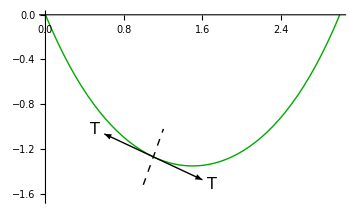

The force will be acting along the rope. It can be proven that, if the rope has no stiffness, any lateral stresses would cause it to twist or bend. We can write the force with which the right part of the cable pulls the left part as T  l^–, where l^– is the unit vector pointing along the cable in the +x direction and T is the tension at that point of the rope. Below is given an illustration of that:

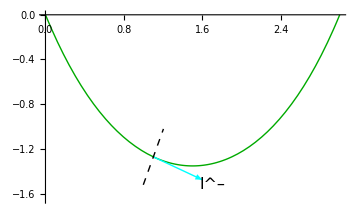

Similarly, the force with which the left part of the cable pulls the left part equals -T  l^–. It is convenient to introduce a new vector T^–,

T^– ≡ T l^–

If we divide the cable in two sections, then the left side would feel the force T^–, and the right side would feel the force -T^–.

#### Code used to generate the illustrations

```mathematica
With[{x0 = 1.1},
	Show[{
			Plot[Cosh[x - 1.5] - Cosh[1.5], {x, 0, 3}, PlotStyle -> {Thick, Darker@Green}],
			Graphics[{
				{Thick, Arrow[{#, # - 0.5{1, Sinh[x0 - 1.5]}}& @ {x0, Cosh[x0 - 1.5] - Cosh[1.5]}]},
				{Thick, Arrow[{#, # + 0.5{1, Sinh[x0 - 1.5]}}& @ {x0, Cosh[x0 - 1.5] - Cosh[1.5]}]},
				{Text[Style["T", 16], {x0, Cosh[x0 - 1.5] - Cosh[1.5]} - 0.6{1, Sinh[x0 - 1.5]}]},
				{Text[Style["T", 16], {x0, Cosh[x0 - 1.5] - Cosh[1.5]} + 0.6{1, Sinh[x0 - 1.5]}]},
				{Dashed, Line[{# + 0.25{Sinh[x0 - 1.5], -1}, # - 0.25{Sinh[x0 - 1.5], -1}}& @ {x0, Cosh[x0 - 1.5] - Cosh[1.5]}]}
			}]
		},
		PlotRange -> {{0, 3}, {1 - Cosh[1.5] - 0.3, 0}},
		ImageSize -> Medium
	]
]
```

```mathematica
With[{x0 =1.1},
	Show[{
			Plot[Cosh[x - 1.5] - Cosh[1.5], {x, 0, 3}, PlotStyle -> {Thick, Darker@Green}],
			Graphics[{
				{Thick, Cyan, Arrow[{#, # + 0.5{1, Sinh[x0 - 1.5]}}& @ {x0, Cosh[x0 - 1.5] - Cosh[1.5]}]},
				{Text[Style["l^–", 16], {x0, Cosh[x0 - 1.5] - Cosh[1.5]} + 0.6{1, Sinh[x0 - 1.5]}]},
				{Dashed, Line[{# + 0.25{Sinh[x0 - 1.5], -1}, # - 0.25{Sinh[x0 - 1.5], -1}}& @ {x0, Cosh[x0 - 1.5] - Cosh[1.5]}]}
			}]
		},
		PlotRange -> {{0, 3}, {1 - Cosh[1.5] - 0.3, 0}},
		ImageSize -> Medium
	]
]
```

### Total force of tension acting on a small piece of rope

Let’s look at a small piece of cable confined between ζ_0 and ζ_0 + dζ.

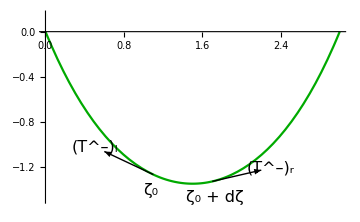
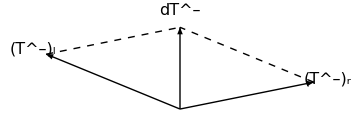

The small piece is being pulled both from the left and from the right; the total force d T^– exerted on it by the rest of the rope then equals (T^–)_l + (T^–)_r. We know that (T^–)_l = -T^–[t, ζ_0] ,   (T^–)_r = T^–[t, ζ_0 + dζ]. Because dζ is infinitesimally small, we have (T^–)_l + (T^–)_r = T^–[t, ζ_0 + dζ] - T^–[t, ζ_0]= (∂T^–)/(∂ζ)dζ.

d T^– = (∂T^–)/(∂ζ)dζ

#### Code used to generate the illustration

```mathematica
With[{x0 = 1.1, dx = 0.6},
	Row[{Show[{
			Plot[Cosh[x - 1.5] - Cosh[1.5], {x, 0, 3}, PlotStyle -> {Thick, Darker@Green}],
			Graphics[{
				{Thick, Arrow[{#, # - 0.5{1, Sinh[x0 - 1.5]}}& @ {x0, Cosh[x0 - 1.5] - Cosh[1.5]}]},
				{Thick, Arrow[{#, # + 0.5{1, Sinh[x0 + dx - 1.5]}}& @ {x0 + dx, Cosh[x0 + dx - 1.5] - Cosh[1.5]}]},
				{Text[Style["ζ_0", 16], {x0 - 0.03, Cosh[x0 - 1.5] - Cosh[1.5] - 0.14}]},
				{Text[Style["ζ_0 + dζ", 16], {x0 + dx + 0.03, Cosh[x0 + dx - 1.5] - Cosh[1.5] - 0.14}]},
				{Text[Style["(T^–)_l", 16], {x0, Cosh[x0 - 1.5] - Cosh[1.5]} - 0.6{1, Sinh[x0 - 1.5]}]},
				{Text[Style["(T^–)_r", 16], {x0 + dx, Cosh[x0 + dx - 1.5] - Cosh[1.5]} + 0.6{1, Sinh[x0 + dx - 1.5]}]}
			}]
		},
		PlotRange -> {{0, 3}, {1 - Cosh[1.5] - 0.14, 0.15}},
		ImageSize -> Medium
	],
	Graphics[{
		{Thick, Arrow[{{0, 0}, -0.5{1, Sinh[x0 - 1.5]}}]}, {Text[Style["(T^–)_l", 16], -0.55{1, Sinh[x0 - 1.5]}]},
		{Thick, Arrow[{{0, 0}, 0.5{1, Sinh[x0 + dx - 1.5]}}]}, {Text[Style["(T^–)_r", 16], 0.55{1, Sinh[x0 + dx - 1.5]}]},
		{Dashed, Line[{-0.5{1, Sinh[x0 - 1.5]}, 0.5{0, Sinh[x0 + dx - 1.5] - Sinh[x0 - 1.5]}}]},
		{Dashed, Line[{0.5{1, Sinh[x0 + dx - 1.5]}, 0.5{0, Sinh[x0 + dx - 1.5] - Sinh[x0 - 1.5]}}]},
		{Arrow[{{0, 0}, 0.5{0, Sinh[x0 + dx - 1.5] - Sinh[x0 - 1.5]}}]}, {Text[Style["dT^–", 16], 0.6{0, Sinh[x0 + dx - 1.5] - Sinh[x0 - 1.5]}]},
	}, ImageSize -> Medium]
	}]
]
```

### Unit tangent vector l^– expressed through ζ^̑, y^̑, h^̑

Let’s say there is a point with coordinates <ζ,y[ζ], h[ζ]> that lies on the rope. Now, let’s change ζ by some small value dζ, so that we are now at the point <ζ + dζ, y[ζ + dζ], h[ζ + dζ]>. By chain rule, the displacement vector is given as d r^– = ((∂r^–)/(∂ζ) + (∂r^–)/(∂y)(∂y)/(∂ζ) + (∂r^–)/(∂h)(∂h)/(∂ζ))dζ; by the definition of ζ^̑, y^̑, and h^̑ (6), this equals

δ r^– = ((ζ^̑)_r + (∂y)/(∂ζ)(y^̑)_r + (∂h)/(∂ζ)(h^̑)_r)dζ

where (ζ^̑)_r[t, ζ] ≡ ζ^̑[ζ, y[t, ζ], h[t, ζ]], and the same is true for (y^̑)_r and (h^̑)_r. We can get the unit tangent vector by normalizing the displacement vector: l^– = (d r^–)/(√(dr^– · d r^–)). Using formulas (7), (8), (9), we get

l^– = ((ζ^̑)_r + (∂y)/(∂ζ)(y^̑)_r + (∂h)/(∂ζ)(h^̑)_r)/(√(f_r^2 + ((∂y)/(∂ζ))^2 + ((∂h)/(∂ζ))^2))

Strictly speaking, -l^– would also be a unit tangent vector. But let’s choose +l^–, as it points in the +x direction. Linearizing this expression, we obtain

l^– = 1/f_r((ζ^̑)_r + (∂y)/(∂ζ)(y^̑)_r + (∂h)/(∂ζ)(h^̑)_r)

## Deriving the equations of motion

### Writing the Newton’s second law

Let’s write the Newton’s second law for a small section A of the rope.

dm (d(v^–)_A)/dt = ∑F^–

Here dm is the mass of  A, (v^–)_A is its velocity vector, and ∑F^– is the total force acting on it. There are two forces acting on A: the force of gravity and the force of tension. The total force of tension exerted on A by the rest of the rope equals d T^– = (∂T^–)/(∂ζ)dζ (26), and the force of gravity is d(F^–)_g = g^– dm; thus, ∑F^– = g^– dm + (∂T^–)/(∂ζ)dζ. According to (20), the length of the piece of rope A is given as dl = f_r dζ, where dζ is the difference between the ζ coordinates of the piece’s front and back ends. The mass of the section equals δm = ρ dl = ρ f_r δζ, where ρ is the linear mass density of the cable. Combining this with the previous equation and cancelling the dζ factor, we get

ρ f_r (d(v^–)_A)/dt = (∂T^–)/(∂ζ) + ρ f g^–

The velocity vector (v^–)_A of the small segment is by definition (v^–)_A ≡ (d(r^–)_A)/dt. By chain rule, (d(r^–)_A)/dt = (∂r^–)/(∂ζ)dζ_A/dt + (∂r^–)/(∂y)dy_A/dt + (∂r^–)/(∂h)dh_A/dt, where ζ_A, y_A, h_A are the coordinates of the small section A. Using the definition of the basis vectors (6), this can be written as

(v^–)_A = (ζ^–)_A dζ_A/dt + (y^–)_A dy_A/dt + (h^–)_A dh_A/dt

where (ζ^̑)_A[t] ≡ ζ^̑[ζ_A[t], y_A[t], h_A[t]] is the value of ζ^̑ at the point <ζ_A, y_A, h_A>, and the same goes for (y^̑)_A and (h^̑)_A. We can take the time derivative of (v^–)_A using the product rule:

(d (v^–)_A)/dt = (ζ^̑)_A(d^2 ζ_A)/dt^2 + (y^̑)_A(d^2 y_A)/dt^2 + (h^̑)_A(d^2 h_A)/dt^2 + (d(ζ^̑)_A)/dt dζ_A/dt + (d(y^̑)_A)/dt dy_A/dt + (d(h^̑)_A)/dt dh_A/dt

Since the basis vectors  are functions of position, their derivatives can be found using the chain rule. For (ζ^̑)_A[t] ≡ ζ^̑[ζ_A[t], y_A[t], h_A[t]], for example, we have (d(ζ^̑)_A)/dt = (∂ζ^̑)/(∂ζ)dζ_A/dt + (∂ζ^̑)/(∂y)dy_A/dt + (∂ζ^̑)/(∂h)dh_A/dt; it is a sum of three terms of the form (∂ζ^̑)/(∂h)dh_A/dt, which are all of order ε. When multiplied with the time derivatives of ζ_A, y_A, h_A, the derivatives of the basis vectors product quadratic terms, which we neglect:

(d (v^–)_A)/dt = (ζ^̑)_A(d^2 ζ_A)/dt^2 + (y^̑)_A(d^2 y_A)/dt^2 + (h^̑)_A(d^2 h_A)/dt^2 + O[ε^2]

Substituting this into Newton’s second law (28) keeping in mind the definition u_A ≡ dζ_A/dt (23), we obtain

ρ f_r ((ζ^̑)_A du_A/dt + (y^̑)_A(d^2 y_A)/dt^2 + (h^̑)_A(d^2 h_A)/dt^2) = (∂T^–)/(∂ζ) + ρ f_r g^–

Because A belongs to the cable, it satisfies y_A = y[t, ζ_A], h_A = h[t, ζ_A], u_A = u[t, ζ_A]. For du_A/dt, we have du_A/dt = d/dt u[t, ζ_A[t]] = (∂u)/(∂t) + (∂u)/(∂ζ)dζ_A/dt; since (∂u)/(∂ζ) and dζ_A/dt are both of order ε, their product is of order ε^2, and we thus have du_A/dt = (∂u)/(∂t)[t, ζ_A] + O[ε^2]. Similarly, we have (d^2 y_A)/dt^2 = (∂^2 y)/(∂t^2)[t, ζ_A] + O[ε^2] and (d^2 h_A)/dt^2 = (∂^2 h)/(∂t^2)[t, ζ_A] + O[ε^2].

ρ f_r((∂u)/(∂t)[t, ζ_A] (ζ^̑)_A + (∂^2 y)/(∂t^2)[t, ζ_A] (y^̑)_A + (∂^2 h)/(∂t^2)[t, ζ_A] (h^̑)_A) = (∂T^–)/(∂ζ) + ρ f_r g^–

Since we haven’t made any assumptions about the position of A, the above equation is true for any small section the cable. To put it another way, it is true for the entirety of the cable.

ρ f_r((∂u)/(∂t) (ζ^̑)_r + (∂^2 y)/(∂t^2)(y^̑)_r + (∂^2 h)/(∂t^2)(h^̑)_r) = (∂T^–)/(∂ζ) + ρ f_r g^–

Because ((∂u)/(∂t) (ζ^̑)_r + (∂^2 y)/(∂t^2)(y^̑)_r + (∂^2 h)/(∂t^2)(h^̑)_r) is of order ε, we only need the zeroth order term in the Taylor expansion of f_r, which equals 1 (9).

ρ ((∂u)/(∂t) (ζ^̑)_r + (∂^2 y)/(∂t^2)(y^̑)_r + (∂^2 h)/(∂t^2)(h^̑)_r) = (∂T^–)/(∂ζ) + ρ f_r g^–

### Writing the equations

To derive the equations of motion, let us combine Newton’s second law (29), the incompressibility condition (24), the condition that the force of tension acts along the rope (25), the formula (27), the formula for the cable’s equilibrium shape (1), and the geometrical identities (7)-(18). We also neglect the O[ε^2] terms, which are quadratic in the cable’s displacement. The derivation is quite long and is given in the uncut version of the work in the chapters “Curvilinear coordinates” and “Introducing small oscillations”. The resulting equations of motion are:

(∂^2 ψ)/(∂τ^2) = ∂/(∂σ)[√(1+σ^2)(∂ψ)/(∂σ)]

∂^2/(∂τ^2)[(1+2 σ^2)/(1+σ^2)η + 4 σ(∂η)/(∂σ) + (1+σ^2)(∂^2 η)/(∂σ^2)] = (1+σ^2)^(3/2)(∂^4 η)/(∂σ^4) + 7 σ √(1+σ^2)(∂^3 η)/(∂σ^3) + (7+10 σ^2)/(√(1+σ^2))(∂^2 η)/(∂σ^2) - (σ (1-2 σ^2))/((1+σ^2)^(3/2))(∂η)/(∂σ) - (2 (1-2 σ^2))/((1+σ^2)^(5/2))η

Here, τ, σ, ψ, η are dimensionless variables which are defined as

σ  ≡  (ζ - l_0)/Λ = Sinh[(x - x_0)/Λ]
τ  ≡  t / √(Λ/g)
ψ ≡ y / Λ
η ≡ h / Λ

where l_0 ≡ Λ Sinh[x_0/Λ]. In terms of these variables, the cable’s equilibrium curvature k_e[ζ] and equilibrium tension T_e[ζ] are given as

k_e[ζ] = 1/Λ 1/(1 + σ^2)
T_e[ζ] = ρ g Λ √(1 + σ^2)

where  ρ is the cable’s linear mass density. And the condition that the cable’s length is equal to L (22) becomes

(∫^σ_p)_σ_0(η[τ, σ] dσ)/(1 + σ^2)= 0

### Formulating the boundary conditions

The cable’s ends are fixed at the points O and P. This means that even if the cable is moving, its endpoints are exactly where they were in equilibrium, and their displacement is equal to zero:

y[t, 0] = y[t, L] = 0
h[t, 0] = h[t, L] = 0

Holding the cable’s ends in place also means that their velocity is zero, and in particular, the rate of change of their ζ coordinates is also zero:

u[t, 0] = u[t, L] = 0

By combining (32) and (35), we get that the boundary conditions for ψ are

ψ[τ, σ_0] = 0
ψ[τ, σ_p] = 0

where σ_0 and σ_p are the coordinates σ of the points O and P, respectively. For η, we also have η[τ, σ_0] = h[τ, σ_p] = 0. And although it might not be immediately obvious, the condition (36) can actually be written in terms of η as

η[τ, σ_0] = 0
η[τ, σ_p] = 0
∂^2/(∂^2 τ)(∂η)/(∂σ) = √(1+σ^2)(∂^3 η)/(∂σ^3) + (4 σ)/(√(1+σ^2))(∂^2 η)/(∂σ^2) + (3+2 σ^2)/((1+σ^2)^(3/2))(∂η)/(∂σ)               σ = σ_0 || σ = σ_p

To write (36) in terms of η, we need to use Newton’s second law, as shown in the uncut version.

## Nonlocality of in-plane oscillations

In an inextensible cable, tension waves propagate with infinite speed - if we, for example, place the cable on the table as a straight line and pull one of its ends, then, due to the in-extensibility condition, the entire cable has to accelerate at once, like a rigid body.  This means that tension has travelled through the cable’s length immediately, with infinite speed. We can also come to this conclusion from the formula for the speed of sound in a uniform isotropic medium, which says that c = √(E/ρ), where E is the material’s Young modulus and ρ is its density. An inextensible cable can be thought of as a cable made from a material with E → ∞; plugging this into the formula for the speed of sound yields c → ∞, which again explains why tension in the cable travels with infinite speed.
	An inextensible cable lying flat on the table is an example of nonlocality. For a hanging catenary cable, in-plane oscillations are coupled with tension - we can see it by observing that since the cable has a positive curvature, increasing the tension would cause some of the cable’s sections to accelerate upward. Because in-plane oscillations are coupled to tension and tension can travel infinitely quickly across an inextensible cable, we would expect in-plane oscillations to travel infinitely quickly as well. In other words, we expect to see nonlocality of in-plane oscillations.
	Nonlocality is of course forbidden by the principle of locality, which is a very general principle in physics; the nonlocality observed in this problem is simply a consequence of the in-extensibility idealization, which does not hold for any real cable. This can be seen from the derivation of (35), which is given in the uncut version; the mixed derivatives in the equation (31) appear precisely when we try to satisfy the in-extensibility condition.

### Empirical observation

To test our hypothesis, let’s look at the qualitative behavior of the equation (31), which describes in-plane oscillations. The equation reads

∂^2/(∂τ^2)[(1+2 σ^2)/(1+σ^2)η + 4 σ(∂η)/(∂σ) + (1+σ^2)(∂^2 η)/(∂σ^2)] = (1+σ^2)^(3/2)(∂^4 η)/(∂σ^4) + 7 σ √(1+σ^2)(∂^3 η)/(∂σ^3) + (7+10 σ^2)/(√(1+σ^2))(∂^2 η)/(∂σ^2) - (σ (1-2 σ^2))/((1+σ^2)^(3/2))(∂η)/(∂σ) - (2 (1-2 σ^2))/((1+σ^2)^(5/2))η

Knowing the cable’s shape η[τ_0, σ] at some instant τ_0, we can calculate the accelerations of its components ∂^2/(∂τ^2)η[τ_0, σ]. Let us denote η_τ0[σ] ≡ η[τ_0, σ] and (η^(··))_τ0[σ] ≡ ∂^2/(∂τ^2)η[τ_0, σ]. In terms of these functions, the equation can be written as

{(1+2 σ^2)/(1+σ^2) + 4 σ d/dσ + (1+σ^2)d^2/dσ^2}(η^(··))_τ0 = (1+σ^2)^(3/2)(d^4 η_τ0)/dσ^4 + 7 σ √(1+σ^2)(d^3 η_τ0)/dσ^3 + (7+10 σ^2)/(√(1+σ^2))(d^2 η_τ0)/dσ^2 - (σ (1-2 σ^2))/((1+σ^2)^(3/2))dη_τ0/dσ - (2 (1-2 σ^2))/((1+σ^2)^(5/2))η_τ0

Since the function η_τ0[σ] is known, the right-hand side of the above equation is also a known function, and (η^(··))_τ0[σ] can be found from an ODE. Here is where nonlocality comes into play. To find acceleration as a function of position (η^(··))_τ0[σ], we have to perform integration. To see that this leads to nonlocality, let us look at the above equation for

η[σ] = B[σ/R - 1/2] - B[σ/R + 1/2]

Here R > 0 is an arbitrary parameter and B is a piecewise polynomial chosen such that B[0] = 1, B[s] = 0 for |s| > 1, and B, B', B'', B''' are continuous (see formula below). Combining two B functions as in (40) gives us a “double pulse”, as illustrated below for R = 1. From the formula, it can be seen that η[σ] = -η[-σ] and η[σ] = 0 for |σ| > 3/2 R. Substituting this into the boundary conditions η[σ_0] = η[σ_p] = 0 (38) and the condition that the cable’s length equals L (34), we see that (40) is valid in that it can describe the shape of a real cable if we make sure that σ_0 < -(3/2)R, σ_p > (3/2)R.

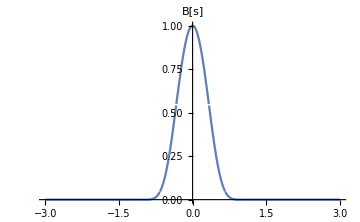
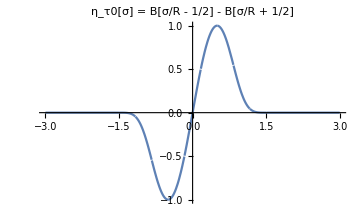

Plugging (40) into the ODE (39), we can find (η^(··))_τ0[σ] numerically with the boundary conditions (η^(··))_τ0[σ_0] = (η^(··))_τ0[σ_p] = 0 (38) using NDSolve. Here is what we get for σ_0 = -5, σ_p = 5, R = 1:

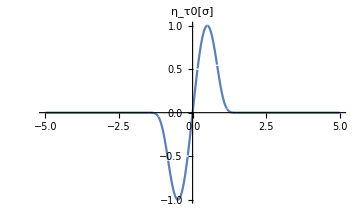
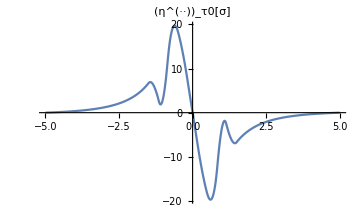

Although η_τ0[σ] is exactly zero for |σ| > 1.5, the cable’s acceleration (η^(··))_τ0 is visibly nonzero outside of that region. What this means is that if we take a small section of the cable and displace it from equilibrium while leaving the rest of the cable in equilibrium configuration and then release the cable, the entirety of the cable starts accelerating immediately at that very moment. A physical explanation is that moving even a small section of the cable from equilibrium changes the tension in the cable, which causes the whole cable to start accelerating.
	The function η given by (40) is a perfectly reasonable function that satisfies all the boundary conditions, is continuous, and has its first three derivatives continuous as well, and the numerical solution given by NDSolve is accurate. We can only conclude from this example that the equation (35) really does lead to nonlocality. A mathematical proof is given in the next subsection.

B[s] ≡ Piecewise[{{B[-s], s < 0}, {1-(54 s^2)/11+(81 s^4)/11, 0 ≤ s < 1/3}, {17/22+(30 s)/11-(189 s^2)/11+(270 s^3)/11-(243 s^4)/22, 1/3 ≤ s < 2/3}, {81/22-(162 s)/11+(243 s^2)/11-(162 s^3)/11+(81 s^4)/22, 2/3 ≤ s < 1}, {0, 1  ≤ s}}]

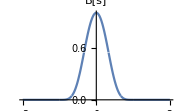
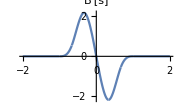
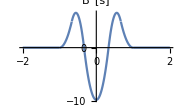
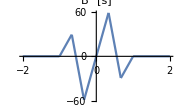

#### Code used to generate the figures

```mathematica
Block[
	{
		Bplus = Function[s, Piecewise[{{1-(54 s^2)/11+(81 s^4)/11, 0 ≤ s < 1/3}, {17/22+(30 s)/11-(189 s^2)/11+(270 s^3)/11-(243 s^4)/22, 1/3 ≤ s < 2/3}, {81/22-(162 s)/11+(243 s^2)/11-(162 s^3)/11+(81 s^4)/22, 2/3 ≤ s < 1}, {0, 1 ≤ s}}]], B, η, R = 1
	},
	B = Function[s, Piecewise[{{Bplus[s], s ≥ 0}, {Bplus[-s], s < 0}}]];
	η = Function[σ, B[σ/R - 1/2] - B[σ/R + 1/2]];
	{Plot[B[s], {s, -3, 3}, PlotLabel -> "B[s]", ImageSize->Medium, PlotRange -> All], Plot[η[σ], {σ, -3, 3}, PlotLabel->"η_τ0[σ] = B[σ/R - 1/2] - B[σ/R + 1/2]", ImageSize->Medium, PlotRange->All]}
]
```

```mathematica
Block[
	{
		R = 1, σ0 = -5, σp = 5,
		RHS, intfunc, soln0, soln1, ηDDot,
		Bplus = Function[s, Piecewise[{{1-(54 s^2)/11+(81 s^4)/11, 0 ≤ s < 1/3}, {17/22+(30 s)/11-(189 s^2)/11+(270 s^3)/11-(243 s^4)/22, 1/3 ≤ s < 2/3}, {81/22-(162 s)/11+(243 s^2)/11-(162 s^3)/11+(81 s^4)/22, 2/3 ≤ s < 1}, {0, 1 ≤ s}}]], B, η
	},
	B = Function[s, Piecewise[{{Bplus[s], s ≥ 0}, {Bplus[-s], s < 0}}]];
	η = B[σ/R - 1/2] - B[σ/R + 1/2];
	
	RHS = (1+σ^2)^(3/2) D[η, {σ, 4}] + 7 σ √(1+σ^2) D[η, {σ, 3}] + (7+10 σ^2)/(√(1+σ^2)) D[η, {σ, 2}] - (σ (1-2 σ^2))/((1+σ^2)^(3/2)) D[η, σ] - (2 (1-2 σ^2))/((1+σ^2)^(5/2))η;
	intfunc = With[{dσ = (σp - σ0)/200}, Interpolation[Table[{s, RHS /. σ -> s}, {s, σ0 - dσ/2, σp + dσ/2, dσ}], InterpolationOrder -> 4]];
	{soln0, soln1} = NDSolve[{
			(1+2 σ^2)/(1+σ^2)a[σ] + 4 σ a'[σ] + (1+σ^2)a''[σ] == intfunc[σ], a[σ0] == 0, a'[σ0] == #
		}, a, {σ, σ0, σp}, MaxStepSize -> 0.001, AccuracyGoal -> 10][[1, 1, 2]]& /@ {0, 1};
	ηDDot = Function[σ, C0 soln0[σ] + C1 soln1[σ]] /. {C0 -> soln1[σp]/(soln1[σp] - soln0[σp]), C1 -> soln0[σp]/(soln0[σp] - soln1[σp])};
	
	{Plot[η, {σ, σ0, σp}, PlotRange -> All, ImageSize -> Medium, PlotLabel -> "η_τ0[σ]"],
	Plot[ηDDot[σ], {σ, σ0, σp}, ImageSize -> Medium, PlotLabel -> "(η^(··))_τ0[σ]", PlotRange -> All]}
]
```

```mathematica
Block[
	{
		Bplus = Function[s, Piecewise[{{1-(54 s^2)/11+(81 s^4)/11, 0 ≤ s < 1/3}, {17/22+(30 s)/11-(189 s^2)/11+(270 s^3)/11-(243 s^4)/22, 1/3 ≤ s < 2/3}, {81/22-(162 s)/11+(243 s^2)/11-(162 s^3)/11+(81 s^4)/22, 2/3 ≤ s < 1}, {0, 1 ≤ s}}]], B, DB, DDB, DDDB
	},
	B = Function[s, Piecewise[{{Bplus[s], s ≥ 0}, {Bplus[-s], s < 0}}]];
	{DB, DDB, DDDB} = Table[D[B[s], {s, d}], {d, 3}];
	{
		Plot[B[s], {s, -2, 2}, PlotRange -> All, ImageSize -> Small, PlotLabel -> "B[s]"],
		Plot[DB, {s, -2, 2}, PlotRange -> All, ImageSize -> Small, PlotLabel -> "B'[s]"],
		Plot[DDB, {s, -2, 2}, PlotRange -> All, ImageSize -> Small, PlotLabel -> "B''[s]"],
		Plot[DDDB, {s, -2, 2}, PlotRange -> All, ImageSize -> Small, PlotLabel -> "B'''[s]"]
	}
]
```

### A mathematical proof

Proof by contradiction. Suppose that the cable’s in-plane oscillations are local. Then, each small section of the cable is directly influenced only by its immediate surroundings. If we take a photo of a small piece of cable at some instant of time, we can determine the acceleration of this small piece of cable by only looking at that small piece and its immediate surroundings. Mathematically, this means that we only need to know the value of η and its derivatives at a particular point to calculate (∂^2 η)/(∂τ^2) at that point:

(∂^2 η)/(∂τ^2)[τ, σ] = F[η[τ, σ], (∂η)/(∂σ)[τ, σ], (∂^2 η)/(∂σ^2)[τ, σ], ...(∂^n η)/(∂σ^n)]

The above expression acts as the equation of motion. It does not contain (∂η)/(∂τ) because of time reversal symmetry - there is no friction in the problem, so the equations of motion should remain invariant when τ is changed to -τ. The equation also does not contain (∂^4 η)/(∂τ^4) or any higher derivatives because Newton’s second law is a second-order differential equation.
	To make better use of (41), we can use the fact that for small oscillations, the equation of motion can be linearized:

(∂^2 η)/(∂τ^2)[τ, σ] = (∑^∞)_(n=0)C_n[σ] (∂^n η)/(∂σ^n)[τ, σ]

Plugging this into (31), we obtain

(1+2 σ^2)/(1+σ^2)(∑^∞)_(n=0)C_n[σ] (∂^n η)/(∂σ^n)[τ, σ] + 4 σ∂/(∂σ)(∑^∞)_(n=0)C_n[σ] (∂^n η)/(∂σ^n)[τ, σ] + (1+σ^2)∂^2/(∂σ^2)(∑^∞)_(n=0)C_n[σ] (∂^n η)/(∂σ^n)[τ, σ] = (1+σ^2)^(3/2)(∂^4 η)/(∂σ^4) + 7 σ √(1+σ^2)(∂^3 η)/(∂σ^3) + (7+10 σ^2)/(√(1+σ^2))(∂^2 η)/(∂σ^2) - (σ (1-2 σ^2))/((1+σ^2)^(3/2))(∂η)/(∂σ) - (2 (1-2 σ^2))/((1+σ^2)^(5/2))η

The right-hand side does not contain fifth or higher order derivatives of η. To make the equation hold in general, the left-hand side cannot contain fifth or higher order derivatives of η, and this means setting C_n = 0 for n > 2. If the left-hand side would contain (∂^5 η)/(∂σ^5), then we would effectively get an equation that tells us (∂^5 η)/(∂σ^5) in terms of η, ...(∂^4 η)/(∂σ^4) - and this of course makes no sense, since the cable’s shape only has to satisfy the boundary conditions. As long as the cable’s ends are held and its length is still L, the shape can be anything, and it’s not restricted by any additional equations.

(∂^2 η)/(∂τ^2)[τ, σ] = C_0[σ]η[σ, τ] + C_1[σ](∂η)/(∂σ)[σ, τ] + C_2[σ](∂^2 η)/(∂σ^2)[σ, τ]

Following the same logic, we conclude that η, ∂/(∂σ)η, ∂^2/(∂σ^2)η, ∂^3/(∂σ^3)η, ∂^4/(∂σ^4)η can be arbitrary. The only way to make the equation hold for a general initial condition η_τ0[σ] is by equating the coefficients before η and all its derivatives. Doing this gives us five equations containing C_0, C_1, C_2 and their first two derivatives; these equations have to be satisfied in order for the formula (41) to make any sense. But we only have three variables C_0, C_1, C_2 to solve a system of five differential equations. The system has no solutions (except for C_0 = C_1 = C_2 = 0), which means that (∂^2 η)/(∂τ^2) cannot be represented through η, (∂η)/(∂σ), (∂^2 η)/(∂σ^2), ... (41). If (∂^2 η)/(∂τ^2) at a point cannot be determined purely from η and its derivatives at that point, then we cannot determine the acceleration of a small piece of the cable by only looking at its immediate surroundings, and the system is thus nonlocal. □

## Dispersion and “continuous reflection”

There is no reason to expect that the normal frequencies of a hanging cable would be rational multiples of each other. What this means is that if we set the cable vibrating, it will not return to its original configuration in any finite amount of time. If we launch a pulse, it will not just bounce back and forth while maintaining its shape, as in the case of a tight string, but will instead deform; this is what we usually call dispersion. And as we know from studying homogenous media with a nonlinear dispersion relation, dispersion can cause pulses to not only “deform” but to also start “radiating backwards”. There is no reason we would expect dispersion in our system to be special in this sense, so the pulses most likely do “reflect backwards” as they travel.
	We can empirically check these two conclusions by numerically solving the equations of motion. For example, let us look at horizontal oscillations with the initial conditions ψ[0, σ] = Exp[-40 σ^2], ∂/(∂τ)ψ[0, σ]  = 0  - this is what happens if we displace the cable from equilibrium and hold it in this position, and then release. The PDE (30) is solved by decomposing ψ[0, σ] into normal modes (see details in uncut version, section “Solving the initial value problem”); although ψ = ⅇ^(-40 σ^2) does not really satisfy the boundary conditions (37), it turns out that the normal mode method automatically takes care of that and replaces ⅇ^(-40 σ^2) with a suitable function. Anyway, here is what we get for ψ[τ, σ] for 0 ≤ τ ≤ 1.8:

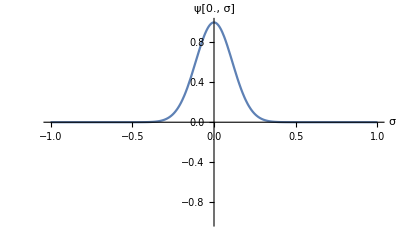
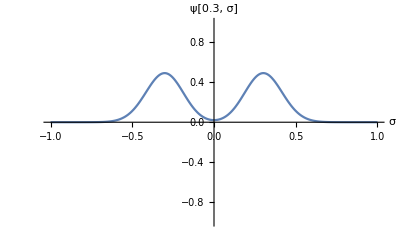
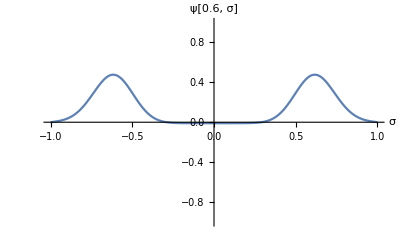
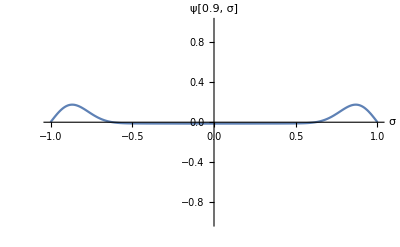
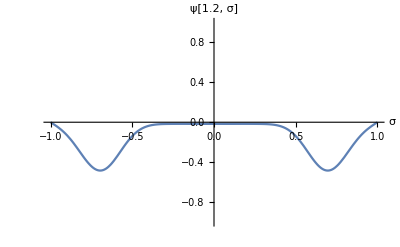
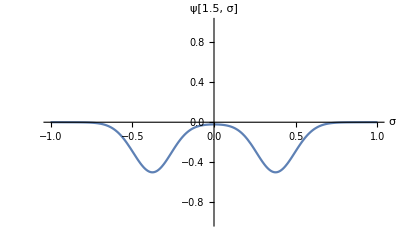
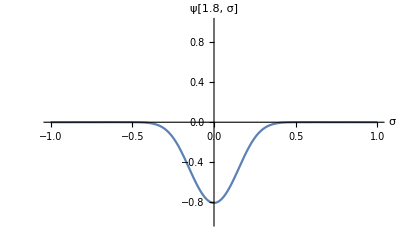

At first, the pulse just “bounces” back and forth, as it would do in a tight string. However, it is evident that after some time, its shape starts to change:

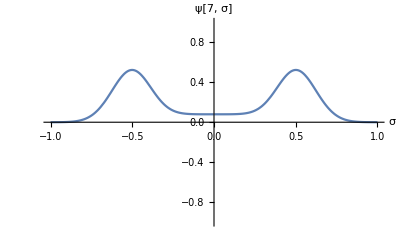

Now, instead of leaving after itself a region with ψ = 0, it leaves a trace. Below, you can see the plot of ψ[τ, σ] for τ = 100. The shape of the original pulse has obviously been distorted.

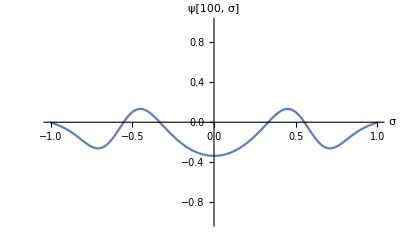

We see that dispersion is indeed present. In addition, it is visible that even after a few bounces, the pulse leaves a “tail” - this illustrates the hypothesis about “continuous reflection”, which is due to the tension in the cable changing with position. We can break the cable into many infinitesimal tight strings with different tension, and in the interface of any two strings, there should be some reflection when a pulse passes - and this is indeed what we see. It would be very interesting to explore this in the future.

## Normal modes of a hanging cable

## Finding the normal modes of horizontal motion

### Writing the normal mode equation for ψ

The equation (30) reads

(∂^2 ψ)/(∂τ^2) = √(1+σ^2)(∂^2 ψ)/(∂σ^2) + σ/(√(1+σ^2))(∂ψ)/(∂σ)

Since it’s a linear equation, its solution is a sum of its normal modes:

ψ[τ, σ] = (∑^∞)_(n = 1)C_n ψ_n[σ] Cos[ϖ_n τ + ϕ_n]

where each of the C_n and ϕ_n is a constant determined by the initial conditions, ψ_n and ϖ_n describe the n-th normal mode of the equation. Substituting this into the equation (30) and using the fact that the normal modes ψ_n are linearly independent, we get, for each normal mode,

√(1+σ^2)(d^2 ψ_n)/dσ^2 + σ/(√(1+σ^2))dψ_n/dσ + ϖ_n^2 ψ_n = 0

### Solving the normal mode equation using Frobenius’s method

In terms of the new variable ξ ≡ √(1 + σ^2) - 1 (idea from John Gregg Gale's master's thesis, 1976), for positive σ, the equation (43) becomes

(1 + ξ)(ϖ^2 ψ + dψ/dξ) + ξ(2 + ξ) (d^2 ψ)/dξ^2 = 0

This is a homogenous linear ODE with polynomial coefficients, so we can solve it using Frobenius’s method near the singular point ξ = 0. The solution is carried out automatically using the function frobeniusDSolve, which is introduced in this Wolfram Community post. The two linearly-independent solutions of (44) are

ψ_((frob)0)[ϖ, ξ] = 1 - ξ ϖ^2 + (ξ^2 ϖ^4)/6 + ...
ψ_((frob)1/2)[ϖ, ξ] = √ξ - 1/12 (1 + 4 ϖ^2)ξ^(3/2) + ...

After finding ψ[ξ], we can find ψ[σ] by substituting ξ = √(1 + σ^2) - 1. When deriving (45) we assumed that σ was positive, but we are also interested in the region σ < 0; thus, we now need to “extend” the solutions to the region σ > 0. For that, let us explore the point σ = 0, where the two regions meet. For σ → 0, we have ξ = √(1 + σ^2) - 1 = σ^2/2 + O[σ^4]. The formula (45) thus becomes

ψ_((frob)0) = 1 - ϖ^2 σ^2/2 + O[σ^4]
ψ_((frob)1/2)  = σ/(√2) + O[σ^3]

If we demand the function ψ and its derivative dψ/dσ to be continuous, we get that ψ_((frob)0) must be an odd function and ψ_((frob)1/2) must be an even function, and here is why. For σ → 0^+, ψ_((frob)0) = 1, d/dσ ψ_((frob)0) = 0; if we demand ψ and dψ/dσ to be continuous at σ = 0, we get that ψ_((frob)0) ≈ 1, d/dσ ψ_((frob)0) ≈ 0 for σ → 0^- as well. We can now construct ψ_((frob)0) by starting from this initial condition near σ = 0 and integrating (43). For σ > 0, we already know what the result is, and it’s given by (45). Let us now change σ to -σ. A quick inspection shows that (43) is invariant under this transformation, and so obviously is the formula ψ_((frob)0) ≈ 1 - ϖ^2 σ^2/2. We see that by flipping σ to -σ we haven’t really changed anything. This implies that ψ_((frob)0) is an even function: ψ_((frob)0)[σ] = ψ_((frob)0)[-σ]. Let us follow a similar argument for ψ_((frob)1/2). Using the fact that for σ → 0^+, ψ_((frob)1/2) = 0, d/dσ ψ_((frob)1/2) = 1 and demanding ψ and dψ/dσ to be continuous at σ = 0, we get that for σ → 0, ψ_((frob)1/2) = 0, d/dσ ψ_((frob)1/2) = 1. We can now construct ψ_1 by starting from this initial condition near σ = 0 and integrating (43). For σ > 0, we already know what the result is, and it’s given by (45). Let us now change σ to -σ. The equation (43) is invariant under this transformation, and the initial condition ψ_((frob)1/2) = 0, d/dσ ψ_((frob)1/2) = 1 changes to ψ_((frob)1/2) = 0, d/dσ ψ_((frob)1/2) = -1; this is exactly the same problem but with a minus sign. Thus, ψ_((frob)1/2) is an odd function: ψ_((frob)1/2)[σ] = -ψ_((frob)1/2)[-σ]. Let us introduce the functions ψ_0 and ψ_1, defined as

ψ_0[ϖ, σ] =ψ_((frob)0)[ϖ, √(1 + σ^2) - 1]
ψ_1[ϖ, σ] = √2 Sign[σ]ψ_((frob)1/2)[ϖ, √(1 + σ^2) - 1]

such that ψ_0[0] =1, d/dσ ψ_0[0] = 0 and ψ_1[0] = 0, d/dσ ψ_1[0] = 1. The functions ψ_0 and ψ_1 are two linearly independent solutions to (43), and a general solution can be found as their superposition:

ψ_n[σ] = C_0 ψ_0[ϖ_n, σ] + C_1 ψ_1[ϖ_n, σ]

Here, n is the node number; it goes from 1 to ∞. In this context, ψ_1[σ], which is the formula (47) with n = 1, must be distinguished from ψ_1[ϖ, σ] (46). While ψ_1[σ] is a normal mode of (30) with a given value of the parameter ϖ that satisfies the boundary conditions, ψ_1[ϖ, σ] is an auxiliary function; these two can be differentiated using the fact that ψ_1 the normal mode has one argument, σ, while ψ_1 the auxiliary function has two arguments, ϖ and σ.
	Frobenius’s method only gives solutions with a finite radius of convergence, so if σ_0 or σ_p are too large, the functions ψ_0 and ψ_1 in (46) have to be found numerically.

### Finding the equation determining the normal frequencies

The formula (47) gives us the general solution of (43). It contains two arbitrary constants C_0 and C_1, whose values must be such that the boundary conditions (37) are satisfied. Substituting (47) into (37), we get a system of equations that can be written in matrix form as

(ψ_0[ϖ, σ_0] | ψ_1[ϖ, σ_0]
ψ_0[ϖ, σ_1] | ψ_1[ϖ, σ_1])(C_0
C_1) = 0

This equation only has nonzero solutions C_0, C_1 when the determinant of the matrix is zero. Denoting it as Ψ[ϖ, σ_0, σ_p], we get that for ψ_n[σ] to be nonzero, the determinant of Ψ must be zero:

Ψ[ϖ, σ_0, σ_p] ≡ (ψ_0[ϖ, σ_0] | ψ_1[ϖ, σ_0]
ψ_0[ϖ, σ_1] | ψ_1[ϖ, σ_1])
det Ψ[ϖ_n, σ_0, σ_p] = 0

Here, ϖ_n is proportional to the n-th normal frequency ω_n as ϖ_n = √(Λ/g)ω_n, which can be seen from the definition of the dimensionless variable τ ≡ t /√(Λ/g) (32), and ψ_0[ϖ, σ] is given by (46). The equation (49) only holds for certain values of ϖ; this is a mathematical formulation of the fact that only some values of ϖ are allowed. In fact, we can use the equation to find the normal frequencies of our system. In the plot below, which shows det Ψ[ϖ, σ_0, σ_p] as a function of ϖ for σ_0 = -1, σ_p = 1, you can see that det Ψ = 0 only for some specific values of ϖ.

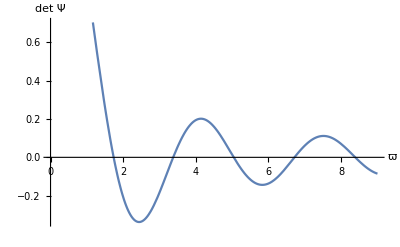

As it is shown in the uncut version, det Ψ[0, σ_0, σ_p] is never zero, and ϖ = 0 is thus not an allowed natural frequency.

## Finding the normal modes of in-plane motion

### Writing the normal mode equation for η

The equation (31) reads

∂^2/(∂τ^2)[(1+2 σ^2)/(1+σ^2)η + 4 σ(∂η)/(∂σ) + (1+σ^2)(∂^2 η)/(∂σ^2)] = (1+σ^2)^(3/2)(∂^4 η)/(∂σ^4) + 7 σ √(1+σ^2)(∂^3 η)/(∂σ^3) + (7+10 σ^2)/(√(1+σ^2))(∂^2 η)/(∂σ^2) - (σ (1-2 σ^2))/((1+σ^2)^(3/2))(∂η)/(∂σ) - (2 (1-2 σ^2))/((1+σ^2)^(5/2))η

Since it’s a linear equation, its solution is a sum of its normal modes:

η[τ, σ] = (∑^∞)_(n = 1)C_n η_n[σ] Cos[ϖ_n τ + ϕ_n]

where each of the C_n and ϕ_n is a constant determined by the initial conditions, η_n and ϖ_n describe the n-th normal mode of the equation. Substituting this into the equation (31) and using the fact that the normal modes η_n are linearly independent, we get

(1+σ^2)^(3/2)(d^4 η_n)/dσ^4 + 7 σ √(1+σ^2)(d^3 η_n)/dσ^3 + (ϖ_n^2(1+σ^2) + (7+10 σ^2)/(√(1+σ^2)))(d^2 η_n)/dσ^2+ (4 ϖ_n^2 σ - (σ (1-2 σ^2))/((1+σ^2)^(3/2)))dη_n/dσ + (ϖ_n^2(1+2 σ^2)/(1+σ^2) - (2 (1-2 σ^2))/((1+σ^2)^(5/2)))η_n = 0

### Solving the normal mode equation using Frobenius’s method

In exactly the same way as with horizontal normal modes, the equation (51) can be re-written in terms of ξ ≡ √(1 + σ^2) - 1 (idea from John Gregg Gale’s master’s thesis, 1976). We can solve the resulting equations using Frobenius’s method near the singular point ξ = 0. Again, the solution is carried out automatically by the function frobeniusDSolve, which is introduced in this Wolfram Community post.

η_((frob)0)[ϖ, ξ] = 1-1/6 ξ^2 (-2+ϖ^2)+1/90 ξ^3 (-36+5 ϖ^2+ϖ^4) + ...
η_((frob)1/2)[ϖ, ξ] = ξ^(1/2) +1/480 ξ^(5/2) (111-68 ϖ^2)+(ξ^(7/2) (-6039+1294 ϖ^2+136 ϖ^4))/20160 + ...
η_((frob)1)[ϖ, ξ] = ξ-1/6 ξ^2 (4+ϖ^2)+1/90 ξ^3 (54+5 ϖ^2+ϖ^4) + ...
η_((frob)3/2)[ϖ, ξ] = ξ^(3/2)-1/20 ξ^(5/2) (13+2 ϖ^2)+(ξ^(7/2) (1843+92 ϖ^2+16 ϖ^4))/3360

After finding ψ[ξ], we can find ψ[σ] by substituting ξ = √(1 + σ^2) - 1. When deriving (52) we assumed that σ was positive, but we are also interested in the region σ < 0; thus, we now need to “extend” the solutions to the region σ > 0. For that, let us explore the point σ = 0, where the two regions meet. For σ → 0, we have ξ = √(1 + σ^2) - 1 = σ^2/2 + O[σ^4]. The formula (52) thus becomes

η_((frob)0) = 1 + O[σ^4]
η_((frob)1/2)  = σ/(√2) + O[σ^4]
η_((frob)1) = σ^2/2 + O[σ^4]
η_((frob)3/2) = σ^3/(2 √2) + O[σ^4]

Now, notice that the functions only have either their value or one of the first three derivatives nonzero at σ → 0^+. Because of the reflection symmetry of the equation (51) around σ = 0 and the condition that the function η[σ] and its first three derivatives must be continuous, the extensions of η_((frob)0) and η_((frob)1) are even functions, while those of ψ_((frob)1/2) and ψ_((frob)3/2) - odd functions.

η_0[ϖ, σ] =η_((frob)0)[√(1 + σ^2) - 1]
η_1[ϖ, σ] = √2 Sign[σ]η_((frob)1/2)[√(1 + σ^2) - 1]
η_2[ϖ, σ] =η_((frob)1)[√(1 + σ^2) - 1]
η_3[ϖ, σ] = (√2)/3 Sign[σ]η_((frob)3/2)[√(1 + σ^2) - 1]

Here, the functions η_0[ϖ, σ], η_1[ϖ, σ], η_2[ϖ, σ], η_3[ϖ, σ] are chosen such that d^p/dσ^p η_(m,p)[0] = δ_mp. These are four linearly independent solutions to (51); a general solution to the equation is their linear combination:

η_n[σ] = C_0 η_0[ϖ_n, σ] + C_1 η_1[ϖ_n, σ] + C_2 η_2[ϖ_n, σ] + C_3 η_3[ϖ_n, σ]

Here, n is the mode number; it goes from 1 to ∞. In this context, η_1[σ], which is the formula (54) with n = 1, must be distinguished from η_1[ϖ, σ] (53). While η_1[σ] is a normal mode of (31) with a given value of the parameter ϖ that satisfies the boundary conditions, η_1[ϖ, σ] is an auxiliary function; these two can be differentiated using the fact that η_1 the normal mode has one argument, σ, while η_1 the auxiliary function has two arguments, ϖ and σ.

### Finding the equation determining the normal frequencies

The formula (54) gives us the general solution of (51). It contains four arbitrary constants C_0, C_1, C_2, C_3, whose values must be such that the boundary conditions (38) are satisfied. Substituting (54) into (38), we get a system of equations that can be written in a matrix form as

(η_0[ϖ, σ_0] | η_1[ϖ, σ_0] | η_2[ϖ, σ_0] | η_3[ϖ, σ_0]
η_0[ϖ, σ_p] | η_1[ϖ, σ_p] | η_2[ϖ, σ_p] | η_3[ϖ, σ_p]
(B^̑)_ϖ η_0[σ_0] | (B^̑)_ϖ η_1[σ_0] | (B^̑)_ϖ η_2[σ_0] | (B^̑)_ϖ η_3[σ_0]
(B^̑)_ϖ η_0[σ_p] | (B^̑)_ϖ η_1[σ_p] | (B^̑)_ϖ η_2[σ_p] | (B^̑)_ϖ η_3[σ_p])(C_1
C_2
C_3
C_4) = 0
(B^̑)_ϖ η ≡ √(1+σ^2)(∂^3 η)/(∂σ^3) + (4 σ)/(√(1+σ^2))(∂^2 η)/(∂σ^2) + ((3+2 σ^2)/((1+σ^2)^(3/2)) + ϖ^2)(∂η)/(∂σ)

As in the case of horizontal oscillations, this equation will only have nonzero solutions C_0, C_1, C_2, C_3 if the determinant of the matrix is zero:

Η[ϖ, σ_0, σ_p] ≡ (η_0[ϖ, σ_0] | η_1[ϖ, σ_0] | η_2[ϖ, σ_0] | η_3[ϖ, σ_0]
η_0[ϖ, σ_p] | η_1[ϖ, σ_p] | η_2[ϖ, σ_p] | η_3[ϖ, σ_p]
(B^̑)_ϖ η_0[σ_0] | (B^̑)_ϖ η_1[σ_0] | (B^̑)_ϖ η_2[σ_0] | (B^̑)_ϖ η_3[σ_0]
(B^̑)_ϖ η_0[σ_p] | (B^̑)_ϖ η_1[σ_p] | (B^̑)_ϖ η_2[σ_p] | (B^̑)_ϖ η_3[σ_p])
det Η[ϖ_n, σ_0, σ_p] = 0

The equation (56) only holds for certain values of ϖ; this is a mathematical formulation of the fact that only some values of ϖ are allowed for normal modes, while some are not. In fact, we can use the equation to find the normal frequencies of our system. Below you can see the plot of det Η as a function of ϖ for σ_0 = -1, σ_p = 1; you can see that det Η is only zero for some specific values of ϖ.

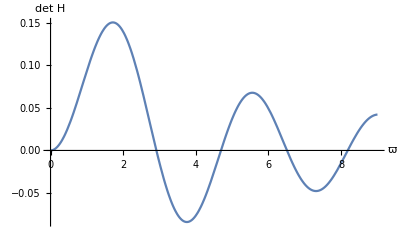

As it is shown in the uncut version, ϖ cannot be zero. Even though det Η[0, σ_0, σ_p] = 0 for any σ_0 and σ_p, ϖ = 0 is impossible because it violates the condition that the cable’s length must be equal to L (see the uncut version).

## Approximate algebraic expression for the natural frequencies and normal modes that gets more accurate as the mode number increases or the cable becomes tighter

### Approximate formula for the normal modes

For a straight wire, we know that the normal modes of horizontal oscillations are precisely ψ[σ] = A Sin[κ(σ - σ_0)], where A and κ are constants. From physical intuition, we would expect to see something similar in a sagging cable. Let us try to solve the normal mode equation for horizontal oscillations (43) as ψ[σ] = A[σ] Sin[ϕ[σ]], with A ≈ const, dϕ/dσ ≈ const.
	Let us denote dϕ/dσ[σ] ≡ κ[σ]. For high-frequency modes, phase changes very rapidly with position, so κ[σ] >> 1. Following the intuition from a tight string, high-frequency normal modes correspond to the limit κ[σ] → ∞. Substituting ψ[σ] = A[σ] Sin[ϕ[σ]] into (43), we arrive at the following equation:

(ϖ^2/κ^2 - √(1+σ^2)) κ^2 A Sin[ϕ] + (σ/(√(1+σ^2))κ A + 2 √(1+σ^2)  κ dA/dσ +√(1+σ^2)dκ/dσ A) Cos[ϕ] + (σ/(√(1+σ^2)) dA/dσ+√(1+σ^2)(d^2 A)/dσ^2)Sin[ϕ] = 0

The first term is of order κ^2; it is much larger than the second term, which is of order κ, which is in turn much larger than the third term, which has no factors of κ in it. Since we are looking for an approximate solution for κ >> 1, we should first equate the first, largest, term to zero. We would then equate the second term to zero and leave the third, smallest, term as it is. This is of course not an exact solution because although the third term is small compared to the other two, it’s nonzero; but this would give us a good approximation. The formula we get by equating the first two terms in (57) to zero is

ψ[σ] ≈ Sin[ϖ σ Hypergeometric2F1[1/4,1/2,3/2,-σ^2] - ϕ_0]/((1+σ^2)^(1/8))
ϕ_0 ≡ ϖ σ_0 Hypergeometric2F1[1/4,1/2,3/2,-σ_0^2]

where ϕ_0 is determined by the boundary condition ψ[σ_0] = 0 (37). The formula makes (58) makes (57) hold up to the O[1] terms, which have no factors of κ in them. Because (57) was obtained from (43) (which is the equation for the normal modes of (30)) by substituting ψ[σ] = A[σ] Sin[ϕ[σ]], the error in (43) is the same as in (57). So, the formula (58) makes the error in (43) a fixed number that doesn’t change as we increase ϖ. Looking at the equation √(1+σ^2)(d^2 ψ)/dσ^2 + σ/(√(1+σ^2))dψ/dσ + ϖ^2 ψ = 0 (43), it is clear that as κ and ϖ get larger, a fixed error in ψ would result in an increasingly large error in the equation. And since we know that the error in (43) is fixed when ψ is given by (58), we conclude that (58) approaches the exact solution to (43) as ϖ → ∞.
	Having found the approximate ψ[σ], we can repeat the same procedure with in-plane oscillations, whose normal modes obey the equation (51). Miraculously, this gives us exactly the same answer as what we got for horizontal oscillations:

η[σ] ≈ Sin[ϖ σ Hypergeometric2F1[1/4,1/2,3/2,-σ^2] - ϕ_0]/((1+σ^2)^(1/8))
ϕ_0 ≡ ϖ σ_0 Hypergeometric2F1[1/4,1/2,3/2,-σ_0^2]

An intuitive explanation for why the normal modes for horizontal and in-plane motion are the same for large ϖ is that the cable’s curvature radius becomes much larger than the normal modes’ characteristic length, which means that the cable can be treated as “locally flat”. And for a flat cable, the normal modes of horizontal and in-plane motion are of course the same.

### Estimating the normal frequencies

We saw that for high ϖ, the normal modes of both (30) and (31) can be approximated as

ψ[σ] ≈ η[σ] ≈ Sin[ϖ σ Hypergeometric2F1[1/4,1/2,3/2,-σ^2] - ϕ_0]/((1+σ^2)^(1/8))
ϕ_0 ≡ ϖ σ_0 Hypergeometric2F1[1/4,1/2,3/2,-σ_0^2]

On the other hand, we know that the cable’s right end is fixed, so ψ[σ_p] = η[σ_p] = 0. To satisfy this condition, the argument of the sine function must be a multiple of π:

ϖ_n (σ_p Hypergeometric2F1[1/4,1/2,3/2,-σ_p^2] - σ_0 Hypergeometric2F1[1/4,1/2,3/2,-σ_0^2]) = n π

This gives us an estimate for the n’th natural frequency of the system for n >> 1:

ϖ_n ≈ π/(σ_p Hypergeometric2F1[1/4,1/2,3/2,-σ_p^2] - σ_0 Hypergeometric2F1[1/4,1/2,3/2,-σ_0^2])n

The expression tells us that for large n, the corresponding ϖ_n’s are evenly spaced.

## Orthogonality of the normal modes of horizontal oscillations

The equation (43) reads

d/dσ[√(1+σ^2)dψ_n/dσ] + ϖ^2 ψ_n = 0

In terms of a new variable χ ≡ ArcSinh[σ], it can be written as

(d^2 ψ_n)/dχ^2 + ϖ_n^2 Cosh[χ]ψ_n = 0

Now, let us look at two normal modes ψ_n and ψ_m.

(d^2 ψ_m)/dχ^2 + ϖ_m^2 Cosh[χ]ψ_m = 0
(d^2 ψ_n)/dχ^2 + ϖ_n^2 Cosh[χ]ψ_n = 0

Multiplying the first equation by ψ_n and the second one by ψ_m, and then integrating, we obtain

(∫^χ_p)_χ_0 ψ_n(d^2 ψ_m)/dχ^2 dχ + ϖ_m^2(∫^χ_p)_χ_0 Cosh[χ]ψ_n ψ_m dχ = 0
(∫^χ_p)_χ_0 ψ_m(d^2 ψ_n)/dχ^2 dχ + ϖ_n^2(∫^χ_p)_χ_0 Cosh[χ]ψ_m ψ_n dχ = 0

where χ_0 ≡ ArcSinh[σ_0], χ_p ≡ ArcSinh[σ_p] are the coordinates χ of the cable’s endpoints. Subtracting the two equations, we have

(ϖ_m^2 - ϖ_n^2)(∫^χ_p)_χ_0 Cosh[χ]ψ_n ψ_m dχ = (∫^χ_p)_χ_0 ψ_m(d^2 ψ_n)/dχ^2 dχ - (∫^χ_p)_χ_0 ψ_n(d^2 ψ_m)/dχ^2 dχ

Using integration by parts and the boundary conditions ψ[χ_0] = ψ[χ_p] = 0 (37), we can show that the right-hand side is zero. If we are talking about two normal modes with different ϖ’s, then the coefficient ϖ_m^2 - ϖ_n^2 is nonzero, and the only way to satisfy the equality is to make the integral itself zero:

(∫^χ_p)_χ_0 ψ_n ψ_m Cosh[χ]dχ = 0                    ϖ_n ≠ ϖ_m

Now, notice that Cosh[χ] dχ is nothing but d Sinh[χ]. Since χ is defined as χ ≡ ArcSinh[σ], we have d Sinh[ArcSinh[σ]] = dσ. Changing variable of integration back to σ, we obtain

(∫^σ_p)_σ_0 ψ_n[σ]ψ_m[σ]dσ = 0                    ϖ_n ≠ ϖ_m

## Lax cable

Let’s look at the case when the cable’s endpoints are brought very close to each other. Intuitively, we would expect the cable to resemble a vertical line. In the figures below, you can see how a cable of length 1 would look like when hung from two points located at the horizontal distance of 0.4, 0.2, 0.1 from each other. The cable’s equilibrium shape indeed approaches a vertical line.

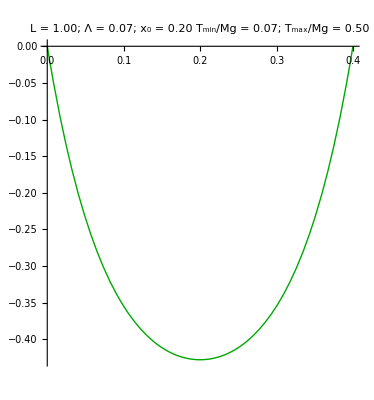
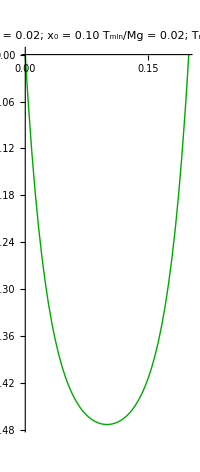
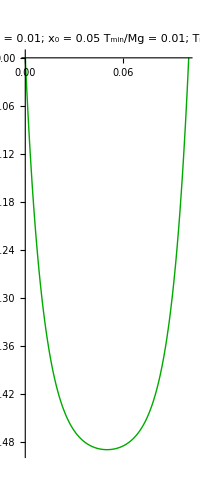

If the cable’s equilibrium shape is almost the same as that of a vertically hung cable, then we would also expect it to oscillate like a vertically hung cable, as in this 2018 UCONN paper. Let us try to quantify this hypothesis. The equations (43) and (51) determining the cable’s normal modes are written as

√(1+σ^2)(d^2 ψ)/dσ^2 + σ/(√(1+σ^2))dψ/dσ + ϖ^2 ψ = 0
(1+σ^2)^(3/2)(d^4 η)/dσ^4 + 7 σ √(1+σ^2)(d^3 η)/dσ^3 + (ϖ^2(1+σ^2) + (7+10 σ^2)/(√(1+σ^2)))(d^2 η)/dσ^2+ (4 ϖ^2 σ - (σ (1-2 σ^2))/((1+σ^2)^(3/2)))dη/dσ + (ϖ^2(1+2 σ^2)/(1+σ^2) - (2 (1-2 σ^2))/((1+σ^2)^(5/2)))η = 0

From the definition σ ≡ (ζ - l_0)/Λ (32) and the fact that ζ goes from 0 to L, we conclude that σ_p - σ_0 = L/Λ. Let us look at the case when the cable’s endpoints are on the same vertical level, such that z_p = 0. From symmetry, σ_0 = -σ_p. Combining this from the previous statement σ_p - σ_0 = L/Λ, we get that σ goes from -L/(2Λ) to +L/(2Λ). Let us denote S ≡ L/2Λ and introduce a new variable ϛ ≡ σ/S, such that σ = S ϛ; this is convenient because the variable ϛ goes from -1 to 1, independently of x_p.
	As x_p → 0, Λ → 0 as well. This can be seen from the formula T_e[σ] = ρ g Λ √(1 + σ^2) (33); the value of T_e is lowest at the point σ = 0, which happens to be the lowest point of the cable. Tension at the lowest point is given by T_(e(min)) = ρ g Λ. Here, ρ is the cable’s linear mass density and g is the free fall acceleration; both parameters are obviously fixed. T_(e(min)) can only change if Λ changes. As we pull the cable’s ends further apart, the tension in the cable is obviously going to increase; conversely, as we bring the cable’s endpoints close together, the tension decreases. Since T_(e(min)) only depends on Λ, this implies that Λ must become smaller as well. From the formula (1) for the equilibrium catenary and the condition z_e[x_p] = z_p that the cable’s right end is fixed at the point P, it can be shown that as x_p → 0, Λ → 0 as well. Now, if Λ → 0 while L stays fixed, then S ≡ L/(2Λ) → ∞.
	The two equations can be written in terms of ϛ as

√(1/S^2+ϛ^2)(d^2 ψ)/dϛ^2 + ϛ/(√(1/S^2+ϛ^2))dψ/dϛ + γ^2 ψ = 0
(1/S^2+ϛ^2)^(3/2)(d^4 η)/dϛ^4 + 7 ϛ √(1/S^2+ϛ^2)(d^3 η)/dϛ^3 + (γ^2(1/S^2+ϛ^2) + (7/S^2+10 ϛ^2)/(√(1/S^2+ϛ^2)))(d^2 η)/dϛ^2+ (4 γ^2 ϛ - (ϛ (1/S^2-2 ϛ^2))/((1/S^2+ϛ^2)^(3/2)))dη/dϛ + (γ^2(1/S^2+2 ϛ^2)/(1/S^2+ϛ^2) - (2 (1/S^2-2 ϛ^2))/(S^2(1/S^2+ϛ^2)^(5/2)))η = 0

where γ^2 ≡ S ϖ^2. As we’ve just shown, S → ∞ for x_p → 0, and this means that 1/S → 0. For |ϛ| >> 1 / S, the equations above can be written as

ϛ(d^2 ψ)/dϛ^2 + dψ/dϛ + γ^2 ψ = 0
d^2/dϛ^2[ϛ^2(ϛ(d^2 η)/dϛ^2 + dη/dϛ + γ^2 ψ)] = 0

Integrating the bottom equation twice, we get

ϛ^2(ϛ(d^2 η)/dϛ^2 + dη/dϛ + γ^2 η) = C_0 + C_1 ϛ

Thus, for a lax cable, the normal modes of both horizontal and in-plane motion are described by basically the same equation:

ϛ(d^2 ψ)/dϛ^2 + dψ/dϛ + γ^2 ψ = 0
ϛ(d^2 η)/dϛ^2 + dη/dϛ + γ^2 η = C_0/ϛ^2 + C_1/ϛ

This is a relatively simple equation that can be solved through Bessel functions:

```mathematica
DSolve[ϛ ψ''[ϛ] + ψ'[ϛ] + γ^2 ψ[ϛ] == 0, ψ, ϛ]
```

{{ψ→Function[{ϛ},BesselJ[0,2 γ √ϛ] C[1]+2 BesselY[0,2 γ √ϛ] C[2]]}}

This is the same as  the equation (16) in the article "Oscillations of a hanging chain" (UCONN, 2018), which looks at the oscillations of a vertically hanging cable. Intuitively, this makes sense: if we bring the cable’s ends close together, then it starts hanging almost vertically, and since it hangs almost vertically, then it  oscillates almost like a vertically hanging cable. Sounds even somewhat obvious when phrased like this.

## Oscillations of a discrete chain

## Kinematics of the chain

Imagine a system (later called the chain) consisting of N + 2 point masses (later called balls) connected without friction by N + 1 massless rigid rods of equal length. The two outmost balls are held in place. How will the chain move under the force of gravity?

### Numbering the balls and defining a coordinate system

First, let’s number the balls. Pick the leftmost and rightmost balls and number them 0 and N + 1, respectively. Number the remaining balls from 1 to N, such that the balls come in order. Below is an example of such numbering for N=12.

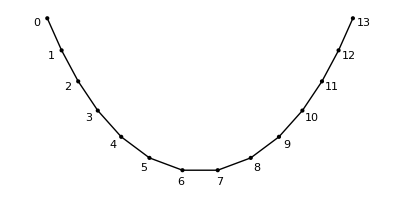

Here, the balls number 0 and N + 1 are held at some fixed points.
	Let us now define a Cartesian coordinate system. First, place the origin at the position of the zeroth ball. Take the z axis to point vertically against the force of gravity, and choose the x axis such that in equilibrium, the chain lies in the x-z plane; finally, take y to be perpendicular to x and z. In other words, just take the coordinate system we’ve used to study a continuous cable. Take the position of the ball N + 1 and call it the point P. Since the ball N + 1 is held in place, the point P is fixed; it’s the same P as in the case of a continuous cable.

### Position of the k-th ball

Any two balls are connected by a rigid rod, so the distance between them equals the length of the rod; all the rods have equal length, so

|(r^–)_k - (r^–)_(k-1)| = λ

where (r^–)_k is the position vector of the k-th ball and λ is the length of one rod. Here, the zeroth ball is located at the origin (or rather, the origin was placed at the position of the zeroth ball), so (r^–)_0 = 0. We can find λ from the fact that the chain’s length is equal to L. If we stretch the chain into a straight line, we would have N + 1 rods each of length λ making a chain of length L. Thus,

λ = L/(N + 1)

(r^–)_k - (r^–)_(k-1) is a vector with three components that has to satisfy the constraint of having length λ; geometrically, it must lie on the surface of a sphere with radius λ. Thus, we can parametrize it using two angles:

(r^–)_k - (r^–)_(k-1) = λ(Sin[ϕ_k] Cos[θ_k]
Sin[ϕ_k]Sin[θ_k]
-Cos[ϕ_k])

-Graphics-

The choice of parametrization is arbitrary, but spherical coordinates are convenient in that the norm of (64) is identically λ. By summing the expression from 0 to k and using the fact that (r^–)_0 = 0, we arrive at the formula for the position vector of the k-th ball.

(r^–)_k = (∑^k)_(n = 1)λ (Sin[ϕ_n] Cos[θ_n]
Sin[ϕ_n]Sin[θ_n]
-Cos[ϕ_n])

The two figures below show the angles θ and ϕ can be used to describe the configuration of the chain.

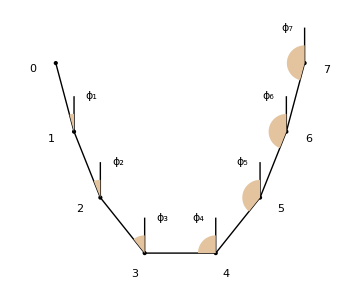
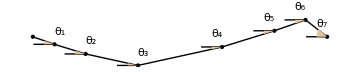
-Graphics-Sight from the +y direction
-Graphics-Sight from above

#### Code used to generate the figures

```mathematica
Table[
	With[{ϕ = 0.9, θ = 0.8}, Rasterize[
		Graphics3D[{
			Arrow[{{0, 0, 0}, {1, 0, 0}}], Text[Style["X", 21], {1.1, 0, 0}],
			Arrow[{{0, 0, 0}, {0, 1, 0}}], Text[Style["Y", 21], {0, 1.1, 0}],
			Arrow[{{0, 0, 0}, {0, 0, 1}}], Text[Style["Z", 21], {0, 0, 1.1}],
			{Thick, Blue, Arrow[{{0, 0, 0}, {Sin[ϕ] Cos[θ], Sin[ϕ] Sin[θ], -Cos[ϕ]}}]},
			{Opacity[0.3], Sphere[{0, 0, 0}]},
			Polygon[Append[Table[{Cos[θ] Sin[α], Sin[θ] Sin[α], -Cos[α]}, {α, 0, ϕ, ϕ/20}], {0, 0, 0}]],
			Polygon[Append[Table[{Sin[ϕ]Cos[α], Sin[ϕ]Sin[α], -Cos[ϕ]}, {α, 0, θ, θ/20}], {0, 0, -Cos[ϕ]}]],
			{FaceForm[], Polygon[({{Cos[θ], 0, -Sin[θ]}, {Sin[θ], 0, Cos[θ]}, {0, -1, 0}}).Append[#, 0] & /@ CirclePoints[50]]},
			{Dashed, Line[{{Sin[ϕ], 0, 0}, {Sin[ϕ], 0, -Cos[ϕ]}}]},
			Text[Style["θ", 16], {0.8Sin[ϕ] Cos[θ/2], 0.8Sin[ϕ] Sin[θ/2], -Cos[ϕ]}],
			Text[Style["ϕ", 16], 0.2{Sin[ϕ] Cos[θ], Sin[ϕ] Sin[θ], -1-Cos[ϕ]}]
		},
		ViewPoint -> viewpoint, Boxed -> False],
		ImageSize -> {600, 600}
	]],
	{viewpoint, {{1.2, 0.4, 0.4}, {0.2, 2.8, 1.4}}}
] // ImageCollage
```

```mathematica
illustrateϕ[xp_, zp_, L_, Nballs_] := Module[
	{
		λ = L / (Nballs + 1),
		plist = { {0, 0} }, glist,
		currx = 0, currz = 0,
		Svals, Cvals
	},
	{Svals, Cvals} = findSC[xp, zp, L, Nballs];
	
	Table[
		currx += λ Svals[[n]];
		currz -= λ Cvals[[n]];
		
		AppendTo[plist, {currx, currz}],
		{n, Length[Svals]}
	];
	
	glist = Point /@ plist;
	
	glist = Join[glist,
		Table[Line[{#[[n]], #[[n + 1]]}], {n, Length[#] - 1}] &@ plist
	];
	
	glist = Join[glist,
		Table[
			Text[
				ToString[n - 1],
				plist[[n]] - λ/3 Normalize[{(Cvals[[#]] + Cvals[[Max[# - 1, 1]]])/2, (Svals[[#]] + Svals[[Max[# - 1, 1]]])/2}]&@ Min[n, Nballs + 1]
			],
			{n, Nballs + 2}
		]
	];
	
	glist = Join[glist,
		Line[{#, # + {0, λ/2}}]& /@ plist[[2;;]],
		Table[
			{RGBColor[0.89, 0.77, 0.62], Polygon[Append[
				Table[plist[[n]] + λ/4{-Sin[a], Cos[a]}, {a, 0, #, # / 20}]&@ If[Svals[[n - 1]]/Cvals[[n - 1]] ≥ 0, ArcTan[Svals[[n - 1]]/Cvals[[n - 1]]], π - ArcTan[-Svals[[n - 1]]/Cvals[[n - 1]]]],
				plist[[n]]
			]]},
			{n, 2, Length[plist]}
		],
		Table[
			Text[
				Subscript["ϕ", n - 1],
				plist[[n]] + λ/2 If[n > Length[plist]/2, {-1/2, 1}, {1/2, 1}]
			],
			{n, 2, Length[plist]}
		]
	];
	
	Labeled[Graphics[glist, ImageSize -> Medium], "Sight from the +y direction"]
]
```

```mathematica
illustrateθ[xp_, zp_, L_, Nballs_] := Module[
	{
		λ = L / (Nballs + 1),
		plist = { {0, 0} }, glist,
		currx = 0, curry = 0,
		Svals, Cvals,
		θlist
	},
	{Svals, Cvals} = findSC[xp, zp, L, Nballs];
	
	θlist = Array[0.3 CubeRoot[Cos[π/(Nballs + 1) #]]&, Nballs];
	AppendTo[θlist, -(θlist.Svals[[;;-2]])/Svals[[-1]]];
	
	Table[
		currx += λ Svals[[n]];
		curry -= λ Svals[[n]] θlist[[n]];
		
		AppendTo[plist, {currx, curry}],
		{n, Length[Svals]}
	];
	
	glist = Point /@ plist;
	
	glist = Join[glist,
		Table[Line[{#[[n]], #[[n + 1]]}], {n, Length[#] - 1}] &@ plist
	];
	
	glist = Join[glist,
		Line[{#, # - {λ/4, 0}}]& /@ plist[[2;;]],
		Table[
			{RGBColor[0.89, 0.77, 0.62], Polygon[Append[
				Table[plist[[n]] + λ/8{-Cos[a], Sin[a]}, {a, 0, θlist[[n - 1]], θlist[[n - 1]] / 20}],
				plist[[n]]
			]]},
			{n, 2, Length[plist]}
		],
		Table[
			Text[
				Subscript["θ", n - 1],
				plist[[n]] + λ/8 If[n > Length[plist]/2, {-1/2, 1}, {1/2, 1}]
			],
			{n, 2, Length[plist]}
		]
	];
	
	Labeled[Graphics[glist, ImageSize -> Medium], "Sight from above"]
]
```

```mathematica
Column[{illustrateϕ[1, 0, 2, 6], illustrateθ[1, 0, 2, 6]}]
```

### Linear approximation

We are only interested in small oscillations near equilibrium. Let us then express the angle ϕ_n in (65) as a sum of its equilibrium value and a small perturbation.

ϕ_n[t] = F_n + φ_n[t]

Here F_n is the value of ϕ_n at equilibrium and φ_n is the small displacement from the equilibrium position. Let us assume that in equilibrium, θ is zero, so that the chain lies in the x-z plane (this is proven in the uncut version, formula 135). Substituting (66) into (65) and taking the first-order approximation, we arrive at the following formula for (r^–)_k:

(r^–)_k = (∑^k)_(n = 1)λ (S_n + C_n φ_n
S_n θ_n
-C_n + S_n φ_n)

Here, S_n ≡ Sin[F_n], C_n ≡ Cos[F_n].

### Boundary conditions

We know that the ball number N + 1 is held at the point P and hence has its <x, y, z> coordinates equal to <x_p, 0, z_p>. Using the formula (67), we get

(∑^(N+1))_(n = 1) (S_n
0
-C_n) + (C_n φ_n
S_n θ_n
S_n φ_n) = (x_p/λ
0
z_p/λ)

## Deriving the equations of motion

### Newton’s second law

Newton’s second law for the k-th ball reads

m (d^2(r^–)_k)/dt^2 = (T^–)_(k, k) + (T^–)_(k+1, k) + m g^–

Here (T^–)_(k, k) and (T^–)_(k+1,  k) is the force with which the rods k and k+1 act upon the ball k, respectively. Let us denote T_k the tension in the k-th rod and (l^–)_k the unit vector pointing along the k-th rod. Since the tension forces act along the rods, we can write the above equation as follows:

m (d^2(r^–)_k)/dt^2 = T_(k+1)(l^–)_(k+1) - T_k(l^–)_k + m g^–

(a proof why tension acts along the rods is given in the uncut version)

### Equations of motion

Combining Newton’s second law (69), the boundary conditions (68), the formula (67) for the position of the k-th ball, and the requirement that the case φ_k = θ_k = 0 corresponds to the chain being in equilibrium, we obtain the following linearized equations of motion:

(θ^(··))_k = -ω_0^2(∑^N)_(n = 1)Y_kn θ_n
(φ^(··))_k = -ω_0^2(∑^(N-1))_(n = 1)K_kn φ_n

The derivation is given in the chapter “Oscillations of a discrete chain” in the uncut version of the work. Here, Y and K are square matrices of dimensions N×N and (N - 1)×(N - 1), respectively; their definition is given below in the formula (71). ω_0 = √(g/L) is a constant; it is a convenient because it only depends on the cable’s length and not on how it’s hung.

Y_kn ≡ (N(N+1))/(μ S_k)Piecewise[{{δ_n1 - δ_n2, k = 1}, {2 δ_nk - δ_(n, k+1) - δ_(n, k-1), 1 < k < N}, {2 δ_nN + S_n/(S_(N+1)) - δ_(n, N-1), k = N}}]                N > 1
Y_11 ≡ 2/μ(1/S_1 + 1/S_2)                                                                                   N = 1
K_kn ≡ (N(N+1))/μ(∑^(N-1))_(s = 1)(M^-1)_ks G_sn
	M_kn ≡ u_nk(S_n - μ/N(k - n)C_n + (C_(k+1))/(S_(k+1))C_n) -  S_n + μ/N(N - n)C_n - (C_(N+1))/(S_(N+1))C_n + (1 + C_N/S_N(C_(N+1))/(S_(N+1)))(N + 1 - n)S_n
	G_kn ≡ Piecewise[{{(2/S_N^3(N + 1 - n) + 1/(S_(N+1))^3(N - n) + 1/S_n^3 δ_(n, N-1))S_n, k = N-1}, {(1/S_N^3(N + 1 - n) + 1/(S_(N+1))^3(N - n) + 1/S_n^3(δ_nk - δ_(n, k+1)))S_n, k < N-1}}]

Here S and C are given by

C_k = (-μ k/N + ν)/(√(1+(-μ k/N + ν)^2))                                    S_k = 1/(√(1+(-μ k/N + ν)^2))

where the parameters μ, ν are found from the equations

(∑^(N+1))_(n = 1) 1/(√(1+(-μ n/N + ν)^2)) = x_p/λ                          (∑^(N+1))_(n = 1) (-μ n/N + ν)/(√(1+(-μ n/N + ν)^2)) = -z_p/λ

### Two simple examples

To verify (70), let us take a chain with a small number of elements and manually compute the normal frequencies. If the result we get matches with what we calculated from (70), then the latter is probably correct.

#### Horizontal oscillations

Let us look at a chain with N = 1, z_p = 0:

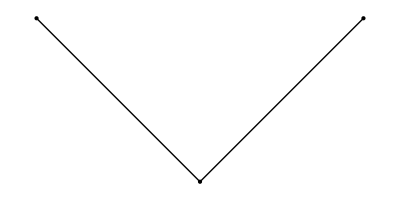

The top two balls are fixed; they are held on the same height, and the horizontal distance between them is x_p. The bottom ball is connected to them via two massless rigid rods of length L/2. The rods are connected with joints. From the picture, it is clear that the system only has one normal mode of oscillations: when the bottom ball is moving into and out of the plane. No in-plane normal modes are present because the system forms a rigid “triangle”.
	From symmetry, the ball can only move in the one vertical plane. Imagining how it would oscillate, it is clear that it would move as a mathematical pendulum with a rod of length √((L/2)^2 - (x_p/2)^2). And as we know, the angular frequency ω of oscillation of such a system is √(g/(√((L/2)^2 - (x_p/2)^2))).
	Let us compute ω for L = 1, g = 1, x_p = 0.5:

```mathematica
With[{L = 1, g = 1, xp = 0.5}, √(g/(√((L/2)^2 - (xp/2)^2)))]
```

1.51967

We want to check the correctness of (70). According to the latter, the angular frequency of the n-th normal mode of in-plane oscillations is given by ω_n = √(g/L λ_n), where λ_n is the n-th eigenvalue of the matrix Y. The function findY[x_p, z_p, L, N] computes the matrix Y using the formula (71), and the code below computes the first normal frequency of in-plane oscillations for L = 1, g = 1, x_p = 0.5 for a chain with N = 1 elements.

```mathematica
With[{L = 1, g = 1, xp = 0.5}, √(g/L First@Eigenvalues[findY[xp, 0, L, 1]])]
```

1.51967

As you can see, the value of ω that we got from (70) is the same as what we’ve calculated manually.

#### Vertical oscillations

Let us now look at a chain with L = 1, N = 2:

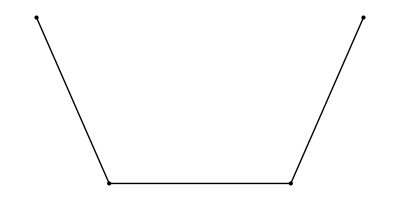

The top two balls are fixed; they are held on the same height, and the horizontal distance between them is x_p. The balls are connected via three massless rigid rods of length l = L/3. The rods are connected with joints. From the picture, it can be seen that the system has one in-plane normal mode. Let us try to find it.
	Denote the angle between the leftmost rod and the vertical as ϕ_1, the angle between the rightmost rod and the vertical - ϕ_2, with ϕ_1 and ϕ_2 taken to be positive in equilibrium. The distance between two bottom balls is l. By the Pythagorean theorem, we have

(x_p - l Sin[ϕ_1] - l Sin[ϕ_2])^2 + (l Cos[ϕ_1] - l Cos[ϕ_2])^2 = l^2

In equilibrium, the chain hangs symmetrically, so ϕ_(1(e)) = ϕ_(2(e)); let’s denote F ≡ ϕ_(1(e)) = ϕ_(2(e)). Demanding the above equality to hold in equilibrium, we obtain x_p/l = 1 + 2 Sin[F]. For small oscillations, the angles ϕ_1 and ϕ_2 only vary by a small amount from their equilibrium value: ϕ_1 = F + φ_1, φ_1 << 1,  and similarly, ϕ_2 = F + φ_2, φ_2 << 1. From the previous equation, we obtain an approximate formula for φ_2 in terms of φ_1:

φ_2 = -φ_1+(1+2 Sin[F]) Tan[F] φ_1^2 + O[φ_1^3]

The Lagrangian of this system is given by L = T - V. The kinetic energy T is the sum of the kinetic energies of the individual balls: T = m/2 v_1^2 + m/2 v_2^2, where v_1 and v_2 are the velocities of the two balls. As it can be seen from the picture, v_1 = l (φ^·)_1 and v_2 = l (φ^·)_2. For the potential energy, we have V = m g z_1 + m g z_2 + C, where z_1 and z_2 are the coordinates z of the two balls and C is an arbitrary constant. As it can be seen from the picture, z_1 = -l Cos[ϕ_1], z_2 = -l Cos[ϕ_2]; let us take C to be 2 m g l Cos[F], so that in equilibrium, V = 0. Substituting the formula for φ_2, which is given above, we arrive at the following formula for the Lagrangian.

L = m l^2 ((φ^·)_1)^2 - m g l 1/2  Sec[F] (2+3 Sin[F]-Sin[3 F])φ_1^2 + O[φ_1^3]

Using the Euler-Lagrange equation, we obtain the equation of motion. Its solution is a sine function with angular frequency

ω = √(3/2 Sec[F] (2+3 Sin[F]-Sin[3 F]) g/L)

where we’ve used the fact that l = L/3. Let us compute ω for L = 1, g = 1, F = π/4:

```mathematica
With[{L = 1, g = 1, F = π/4}, N@√(3/2 Sec[F] (2+3 Sin[F]-Sin[3 F]) g/L)]
```

2.69122

We want to check the correctness of (70). According to the latter, the angular frequency of the n-th normal mode of in-plane oscillations is given by ω_n = √(g/L λ_n), where λ_n is the n-th eigenvalue of the matrix K. The function findK[x_p, z_p, L, N] computes the matrix K using the formula (71), and the code below computes the first normal frequency of in-plane oscillations for L = 1, g = 1, F = π/4 for a chain with N = 2 elements. Here, x_p is set equal to (1 + 2 Sin[F])/3 L to satisfy the condition that the distance between the two oscillating balls is l.

```mathematica
With[{L = 1, g = 1, F = π/4}, √(g/L First@Eigenvalues[findK[(1 + 2 Sin[F])/3 L, 0, L, 2]])]
```

2.69122

As you can see, the value of ω that we got from (70) is the same as what we calculated manually. Thus, the equations (70) are most likely correct.

## From small N to large; comparing to a continuous cable

### Equilibrium configuration

Let us compare the equilibrium shape of a hanging chain to those of a hanging cable. We can do that by computing both shapes and drawing them on top of each other. Below are given some examples for N = 2, 4, 8, 12, with L = 2, x_p= 1, z_p = 0. You can see that although the chain’s shape is initially rather far from the green line representing the cable, as N increases, the shape of the chain comes closer and closer to the catenary.

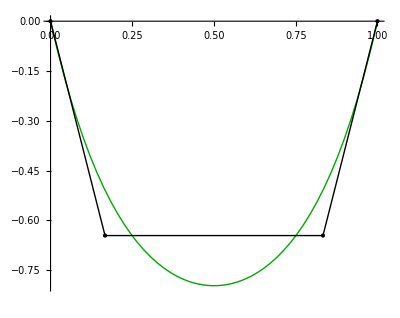
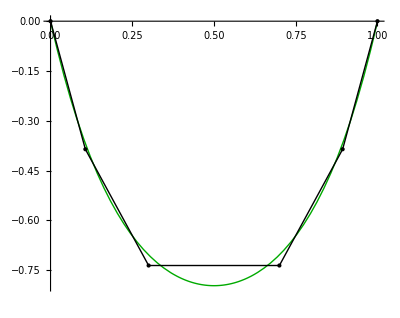
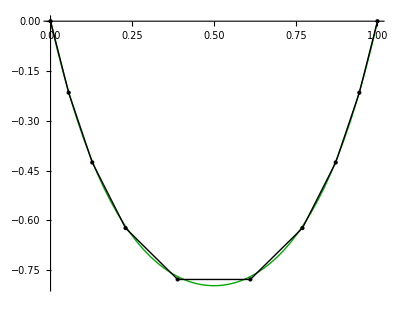
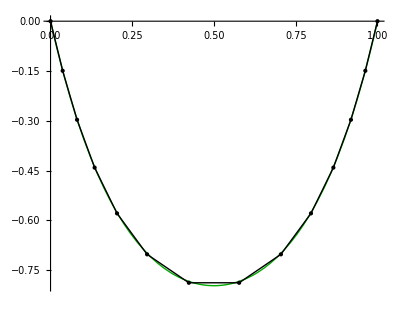

There is an intuitive explanation for that. The potential energy of the chain in the gravitational field is given by U = (∑^N)_(k = 1)m g z_k, where z_k is the z coordinate of the k-th ball. For large N, this sum can be approximated as an integral, and so the potential energy of a hanging chain becomes the same as that of a continuous cable. Next, using the principle of minimum potential energy, we can show that this means that the shape of a chain with a large number of elements is the same as that of a cable.

### Eigenvalues of Y and K and the normal frequencies

The chain’s oscillations are described by the formula (70). Here, the matrix Y and the angles θ_k, 1 ≤ k ≤ N describe the chain’s horizontal oscillations, and the matrix K and the angles φ_k, 1 ≤ k ≤ N - 1 describe the chain’s in-plane oscillations.

(θ^(··))_k = -ω_0^2(∑^N)_(n = 1)Y_kn θ_n
(φ^(··))_k = -ω_0^2(∑^(N-1))_(n = 1)K_kn φ_n

From here, the normal frequencies of horizontal oscillations are given by ω_n = ω_0 √λ_n, where λ_n is the n-th eigenvalue of the matrix Y, and the same applies to in-plane oscillations. The hypothesis is that a chain with a  large number of elements would behave in exactly the same way as a continuous cable, so the frequencies of the normal modes must match, too. While the frequency of the first normal mode of a chain with two free elements will be quite different from that of a continuous cable, the frequency of the first normal mode of a chain with one hundred elements should be very close. As N gets larger, the frequencies of the normal modes should approach a certain limit, which is the frequency of oscillations of a continuous cable. And because ω_n = ω_0 √λ_n, this also means that the eigenvalues λ_n of the matrices Y and K should approach some fixed limits as N → ∞. Combining it with the fact that the normal modes of a continuous cable are written in terms of dimensionless variables (32) as y[ζ, t] = Λ ψ_n[(ζ - l_0)/Λ] Cos[t/√(Λ/g) ϖ_n] and h[ζ, t] = Λ η_n[(ζ - l_0)/Λ] Cos[t/√(Λ/g) ϖ_n], we arrive at the following conjecture:

λ_n → L/Λ ϖ_n^2                          as N → ∞

We can check this empirically by actually computing the matrices Y and K for various values of N and plotting their eigenvalues as a function of N. The horizontal axis here is N; this is because the matrices Y and K describe the oscillations of a chain with a given number of elements N, and of course the oscillations would be different for chains with different number of elements. In this sense, the matrices Y and K are functions of N. For each value of N, we can also compute the eigenvalues of these matrices, and they two will be functions of N. The plots below show the fist four eigenvalues of Y and K as a function of N.

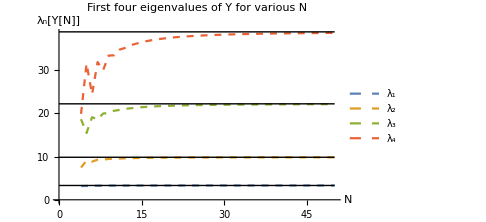
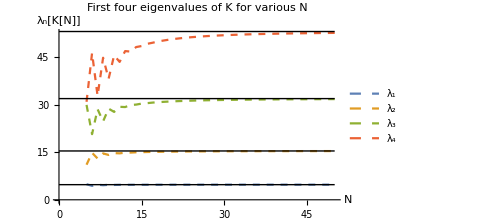

From the two plots above, you can see that the eigenvalues actually do asymptote to the values predicted by (74), shown as black lines. An interesting observation is that the eigenvalues of the K matrix are slightly higher than those of Y, meaning that in-plane oscillations typically have a higher frequency than horizontal oscillations. Also, note that the eigenvalues of the matrices oscillate: the fourth eigenvalue of Y, for example, is large for odd N and small for even N. The fourth eigenvalue of K is large for even N and small for odd N. For N = 4, the third and fourth eigenvalues of Y are almost equal (and so are the natural frequencies of horizontal oscillations), and for N = 5, the third and fourth eigenvalues of K are almost equal as well (and so are the natural frequencies of in-plane oscillations). Is there an explanation for that?

#### Code used to generate the last two figures

```mathematica
Block[
	{
		lines = {{}, {}, {}, {}},
		eigvals
	},
	
	Table[
		eigvals = Reverse@Eigenvalues[findY[1, 0, 2, Nballs]][[-4;;]];
		Table[
			lines[[l]] = Append[lines[[l]], {Nballs, eigvals[[l]]}],
			{l, 4}
		],
		{Nballs, Range[4, 50]}
	];
	
	ListLinePlot[lines, PlotLegends -> {"λ_1", "λ_2", "λ_3", "λ_4"}, AxesLabel -> {"N", "λ_n[Y[N]]"}, PlotLabel -> "First four eigenvalues of Y for various N"]
]
```

```mathematica
Block[
	{
		lines = {{}, {}, {}, {}},
		eigvals
	},
	
	Table[
		eigvals = Reverse@Eigenvalues[findK[1, 0, 2, Nballs]][[-4;;]];
		Table[
			lines[[l]] = Append[lines[[l]], {Nballs, eigvals[[l]]}],
			{l, 4}
		],
		{Nballs, Range[5, 50]}
	];
	
	ListLinePlot[lines, PlotLegends -> {"λ_1", "λ_2", "λ_3", "λ_4"}, AxesLabel -> {"N", "λ_n[K[N]]"}, PlotLabel -> "First four eigenvalues of K for various N"]
]
```

```mathematica
Block[
	{
		xp = 1, zp = 0, L = 2,
		lines = {{}, {}, {}, {}},
		eigvals,
		asymptotes,
		Λ, x0, σ0, σp, ϖ
	},
	Λ = findLambda[L, xp, zp];
	x0 = findX0[L, xp, zp, Λ];
	σ0 = Sinh[-x0/Λ]; σp = Sinh[(xp - x0)/Λ];
	ϖ = findψNmodes[σ0, σp, 4][[All, 1]];
	asymptotes = L/Λ ϖ^2;
	
	Table[
		eigvals = Reverse@Eigenvalues[findY[xp, zp, L, Nballs]][[-4;;]];
		Table[
			lines[[l]] = Append[lines[[l]], {Nballs, eigvals[[l]]}],
			{l, 4}
		],
		{Nballs, Range[4, 50]}
	];
	
	Show[{
		ListLinePlot[lines,
			PlotLegends -> {"λ_1", "λ_2", "λ_3", "λ_4"},
			AxesLabel -> {"N", "λ_n[Y[N]]"}, 
			PlotLabel -> "First four eigenvalues of Y for various N",
			PlotStyle -> {{Thick, Dashed}}
		],
		Graphics[{Thin, Black, Line[{{0, #}, {50, #}}]}& /@ asymptotes]
	}]
]
```

```mathematica
Block[
	{
		xp = 1, zp = 0, L = 2,
		lines = {{}, {}, {}, {}},
		eigvals,
		asymptotes,
		Λ, x0, σ0, σp, ϖ
	},
	Λ = findLambda[L, xp, zp];
	x0 = findX0[L, xp, zp, Λ];
	σ0 = Sinh[-x0/Λ]; σp = Sinh[(xp - x0)/Λ];
	ϖ = findηNmodes[σ0, σp, 4][[All, 1]];
	asymptotes = L/Λ ϖ^2;
	
	Table[
		eigvals = Reverse@Eigenvalues[findK[xp, zp, L, Nballs]][[-4;;]];
		Table[
			lines[[l]] = Append[lines[[l]], {Nballs, eigvals[[l]]}],
			{l, 4}
		],
		{Nballs, Range[5, 50]}
	];
	
	Show[{
		ListLinePlot[lines,
			PlotLegends -> {"λ_1", "λ_2", "λ_3", "λ_4"},
			AxesLabel -> {"N", "λ_n[K[N]]"}, 
			PlotLabel -> "First four eigenvalues of K for various N",
			PlotStyle -> {{Thick, Dashed}}
		],
		Graphics[{Thin, Black, Line[{{0, #}, {50, #}}]}& /@ asymptotes]
	}]
]
```

## Conclusion

## Comparing the numerical results to another article’s

### Natual frequencies of horizontal oscillations

The problem discussed in this work has been explored by John Gregg Gale in his 1976 master's thesis. The methods he used in his work are very different from those used here, however, he also happened to use the same definition of ϖ’s, which he called “natural frequency ratios”. At the end of the article, he provides a series of tables containing the results he obtained for various natural frequencies. We can use this as a reference to confirm the correctness of the present work.
	To make the comparison, let us use the first table for horizontal oscillations:

Here is the same table computed based on the results of this work, with the appropriate parameters L, x_p, z_p calculated from Gale’s support parameter and sag parameter:

(3.64 | 7.23 | 10.84 | 14.44 | 18.05 | 21.65
2.79 | 5.51 | 8.25 | 11.00 | 13.74 | 16.48
1.91 | 3.74 | 5.59 | 7.44 | 9.29 | 11.15
1.51 | 2.92 | 4.36 | 5.80 | 7.24 | 8.69
1.27 | 2.41 | 3.60 | 4.78 | 5.97 | 7.17
1.09 | 2.05 | 3.06 | 4.07 | 5.08 | 6.09
0.96 | 1.78 | 2.65 | 3.52 | 4.39 | 5.26
0.76 | 1.37 | 2.04 | 2.71 | 3.38 | 4.05
0.62 | 1.06 | 1.60 | 2.11 | 2.63 | 3.16)

You can see that the two tables are practically identical. Although some entries sometimes vary by around 0.01, the results to match very closely. The values of ϖ predicted by this work are thus, up to a numerical error, equal to those of John Gregg Gale.

### Natural frequencies of vertical oscillations

Here is Gale’s first table giving the natural frequencies of in-plane oscillations:

And here is the same table computed based on the results of this work:

(6.67 | 9.91 | 13.80 | 17.11 | 20.81 | 24.17
4.52 | 6.92 | 9.61 | 11.99 | 14.56 | 16.95
3.55 | 5.58 | 7.75 | 9.70 | 11.78 | 13.73
2.98 | 4.78 | 6.63 | 8.33 | 10.11 | 11.81
2.59 | 4.23 | 5.87 | 7.40 | 8.97 | 10.49
2.45 | 4.02 | 5.59 | 7.05 | 8.55 | 9.99
2.30 | 3.82 | 5.31 | 6.70 | 8.13 | 9.51
2.09 | 3.50 | 4.87 | 6.16 | 7.48 | 8.75
1.94 | 3.28 | 4.57 | 5.79 | 7.02 | 8.23
1.34 | 2.35 | 3.31 | 4.22 | 5.12 | 6.02
0.98 | 1.76 | 2.50 | 3.21 | 3.91 | 4.60
0.74 | 1.33 | 1.92 | 2.47 | 3.02 | 3.56)

You can see that again, the two tables are practically identical. The difference between this essay’s and John Gregg Gale’s ϖ’s is largest for the sixth normal frequency for the middle rows, when the convergence radius of Frobenius’s method solutions becomes insufficient and numerical solutions have to be used. We can be quite confident that the error does not lie in the equation (31) because the predicted ϖ’s match with Gale’s for both high ϖ’s, when the accurate Frobenius’s method is used, and for low ϖ’s, when NDSolve can provide sufficient accuracy. Thus, we conclude that the values of ϖ predicted by the current work are, up to a numerical error, equal to those predicted by John Gregg Gale. Since the predictions are extremely unlikely to match by accident, we may conclude that the results presented in this work are correct.

## Novelty and relevance of the work

### Novel things presented in the work

A big advantage of the present work compared to past articles is that many interactive visualizations were developed. The reader can experiment with the cable’s or chain’s parameters and see, visually, the system’s equilibrium and modes of oscillation. This makes the content much more intuitive and easy to understand, in addition of course to being entertaining. The demonstrations can be used in classes to illustrate the notion of a normal mode on a system more realistic than a slowly vibrating tight string (in real life, tight strings, such as guitar stings, are in fact so tight that their oscillations are too fast to see) and less complicated than a circular drum. A heavy rope hung between two poles is a very cheap and reliable demonstration and is also thus more practical than many other demonstrations.
	The current work also studies the oscillations of a discrete chain and compares them to those of a continuous cable - something I haven’t seen in other articles. It is interesting to see how a discrete chain approaches a continuous cable as the number of members increases because this touches a very relevant question of how discrete systems with a large number of elements behave. Water, which is made of lots of small molecules, at human scale behaves as if it were continuous. A quantum harmonic oscillator, which has discrete energy levels, does not however have the same thermal energy as its classical analog. A chain with a large number of elements oscillates like a continuous cable. But the emission of thermal radiation happens very differently for atoms with continuous and discrete energy spectra - the “ultraviolet catastrophe”. Sometimes the behavior of discrete systems does approach some limits, sometimes it doesn’t - there probably is not a general principle yet. Maybe, by looking at many examples of how discrete systems do or do not approach some limit we can deduce a general rule?

### Intersections with (and differences from) past works

The problem of an oscillating cable (or a chain, as it’s sometimes called) has been studied in a number of past articles. Perhaps one of the most comprehensive ones available for free is John Gregg  Gale’s master's thesis, written in 1976 in Oregon State University. The author uses methods that are quite different from those used in this work: while the current work describes the cable’s shape through h and y only, Gale’s thesis also makes use of variables representing the cable’s longitudinal displacement and angles. As a result, Gale’s derivation of the equations of motion depends on visual intuition more than the derivation given here, and the equations of motion are written not as two PDEs with one PDE corresponding to one variable but as multiple PDEs of lower order involving not only the cable’s normal displacement but also other variables such as its longitudinal displacement and angles. Each of the resulting equations is shorter than (30) and (31) and hence is somewhat simpler. The equations (30) and (31), however, might be more transparent in that since they only contain y and h, it can be easier to see how the system oscillates - for instance, it’s probably much easier to see how the cable would oscillate if plucked using the equation (31) than using a collection of connected PDEs.
	In Gale’s article, the normal modes of in-plane motion are found in terms the cable’s longitudinal displacement, while in the current work they are found in terms of the cable’s tangential displacement. The approach used in this work has the advantage of being easily visualizable: having found the function h[ζ], we can directly use it to draw the normal mode; having found the tangential displacement as a function of position, however, we have to perform some mathematical manipulations with the result to be able to draw the normal mode.
	Gale coordinatizes the cable through arc length; the work, on the other hand, introduces a curvilinear coordinate system fitted to the cable’s equilibrium. This difference in coordinates is another difference between the current work and Gale’s thesis.
	In his 1953 paper, David Saxon and A. S. Cahn “Modes of vibration of a suspended chain” described an approximate algorithm for finding the normal frequencies of in-plane oscillations. The current article also gives a method for estimating the normal frequencies, namely the formula (60). The formula presented in this work is derived in a comparatively simple way, namely by assuming ψ[σ] and η[σ] to be approximately sinusoidal at a given small interval; the derivation of the formula given by Saxon and Cahn’s article, on the other hand, is quite complicated and involves several pages. It does not, however, contain hypergeometric function as (60) does, so it’s too, in some sense, simpler.
	It is interesting to mention articles on phenomena like conductor galloping, which is when a long electric cable oscillates due to wind, and oscillations of stay bridges. Although the phenomena are in many ways different to the idealized problem discussed in this work, one similarity is that they, too, involve fourth-order partial differential equations. One possible explanation is that maybe, in a cable-type system where both tension and tangential velocity vary, to obtain equations of motion written in terms of tangential displacement only we have to use some conditions, and using them involves differentiation; since we have to take care of two fields, tension and tangential velocity, we differentiate twice and thus end up turning a second-order wave-type equation into a fourth-order PDE. This question would be interesting to explore in future articles.

## Qualitative patterns in the cable’s normal modes

### Greater curvature and amplitude at the lowest point

Here is how the twelfth normal modes of horizontal and in-plane oscillations look like for σ_0 = -8, σ_p = 8:

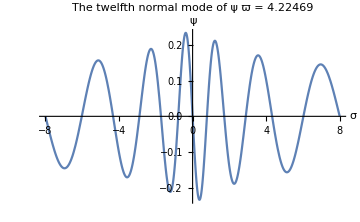
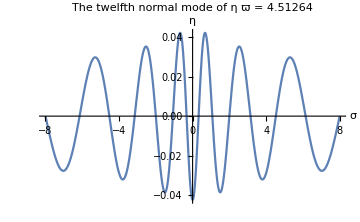

Notice an interesting pattern here: the normal modes oscillate much faster (have a greater curvature) near σ = 0 then at the edges, and the amplitude of the oscillations is also larger at the middle. This also holds true for different values of σ_0, σ_p and different mode numbers. Here is another example, with σ_0 = -4, σ_p = 9:

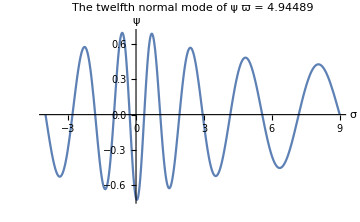
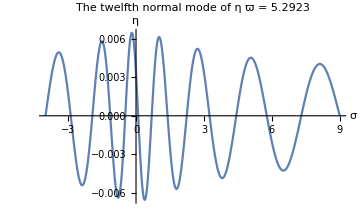

We again see the same thing happening. But why is that? An intuitive explanation goes as follows. Tension in the cable is smallest at the cable’s lowest point, which happens to be the point σ = 0. In a normal mode, the cable oscillates such that at any moment, the acceleration of a piece of cable is proportional to its displacement - we can see it from the formula y[t, ζ] = y[ζ] Cos[ω t], which implies (∂^2 y)/(∂t^2) = -ω^2y. But from Newton’s second law we also know that the acceleration would be a function of the cable’s curvature and tension - more precisely, the acceleration would increase with tension and curvature. Combining the two conclusions, we see that since tension is lowest in the middle, the curvature of the normal modes must be really high to compensate for that - and this is what we observe in the plots above. The explanation for why the normal modes’ amplitude is greater at the middle is that intuitively, we know that it’s more difficult to get a tight string to oscillate than a string with a small tension. A string with a smaller tension would oscillate more than a string with a higher tension if equal driving force were applied. This is of course a somewhat hand-wavy argument; an alternative explanation is given in the section "Approximate algebraic expression for the natural frequencies and normal modes that gets more accurate as the mode number increases or the cable becomes tighter".

### Parity

If the boundary conditions are symmetric, the normal modes of both horizontal and in-plane oscillations respect parity. Here are some examples:

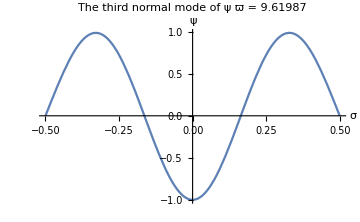
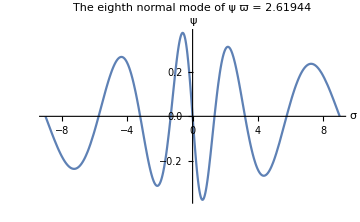
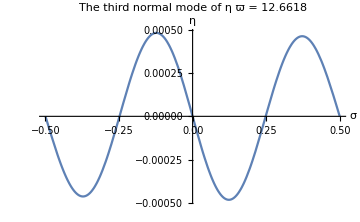
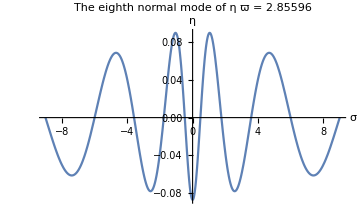
-Graphics- | -Graphics-
-Graphics- | -Graphics-

As long as σ_0 = -σ_p, the normal modes are either even or odd. Intuitively, this makes sense: the equations (30) and (31) are symmetric with respect to σ = 0, and as long as boundary conditions do not introduce asymmetry, it makes sense that the normal modes must respect parity. If σ_0 ≠ -σ_p, however, we see that parity is violated:

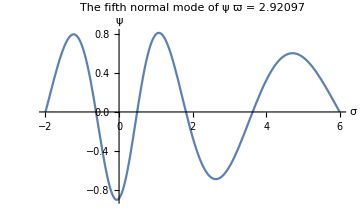

## Qualitative patterns in the chain’s normal modes

In the sections “From small N to large; comparing to a continuous cable” and “Comparing the normal modes as N → ∞, we saw that a chain with a large number of elements oscillates very much like a continuous cable. And indeed, the normal modes tend to have greater “curvature” at the lowest point, and they too have the parity property if the chain is hung symmetrically, as you can see from the two illustrations below.

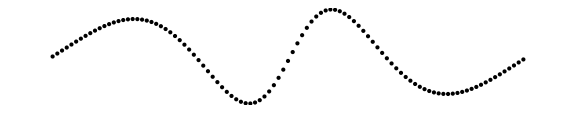
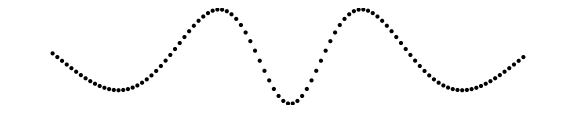
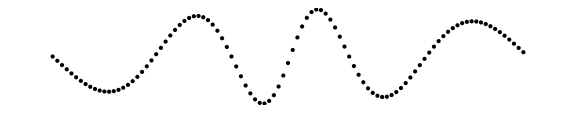

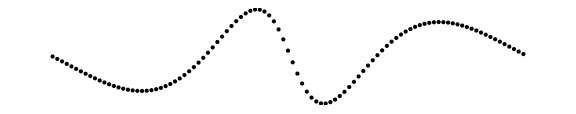
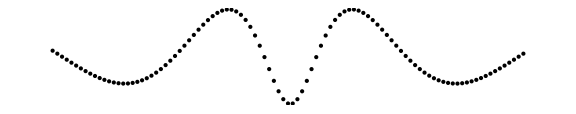
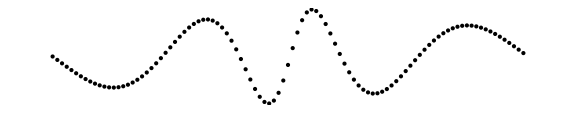

For z_p ≠ 0, you see that parity no longer holds:

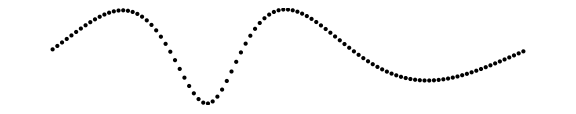
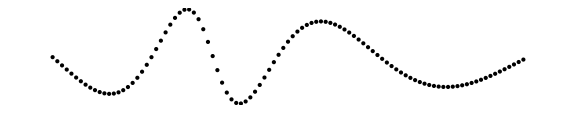
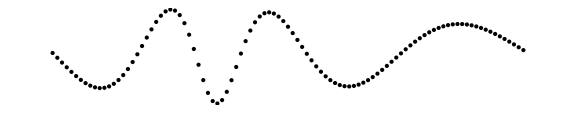

## Open questions

The formula (61) tells us that the normal modes of horizontal oscillations are orthogonal. We also know that the normal modes of a tight string are orthogonal, as well. Is there a general principle or an intuitive explanation for this?
	The equations (43) and (51) take a particularly simple form when written in terms of χ ≡ ArcSinh[σ] and ξ ≡ √(1 + σ^2) - 1: when written in terms of χ, (43) simplifies to (d^2 ψ_n)/dχ^2 + ϖ_n^2 Cosh[χ]ψ_n = 0, and in (51), the coefficient before η becomes zero, effectively reducing it to a third-order equation; when written in terms of ξ, both (43) and (51) have polynomial coefficients. Incidentally, the coordinates χ and ξ also happen to be, up to a linear transformation, Cartesian coordinates. By definition, σ ≡ Sinh[(x - x_0)/Λ], so ξ = (x - x_0)/Λ, which is the horizontal displacement from the cable’s lowest point divided by Λ. By substituting σ = Sinh[(x - x_0)/Λ] into ξ = √(1 + σ^2) - 1, we get ξ = Cosh[(x - x_0)/Λ] - 1. But the formula for z_e[x], which describes the cable’s equilibrium shape, is z_e[x] = Λ Cosh[(x - x_0)/Λ] -Λ Cosh[x_0/Λ]; thus, ξ[x] = (z_e[x] - z_e[x_0])/Λ. In other words, ξ is the vertical displacement from the cable’s lowest point. How did it happen that the equation of motion are most simply written in terms of these coordinates? Maybe every system has some “natural coordinates” that can be guessed from physical intuition in which the equations of motion are written in a most simple form?
	Empirically one can observe that the natural frequencies of in-plane motion are, for a given cable, larger than those of horizontal motion. Why is that? Is there a simple explanation?

## References

The University of Utah, “Systems of differential equations”, http://www.math.utah.edu/~gustafso/2250systems-de.pdf
John Gregg Gale, Oregon State University, master’s thesis, 1976, https://ir.library.oregonstate.edu/downloads/6395w964x
UCONN, 2018, https://www.phys.uconn.edu/~rozman/Courses/m3410_18s/downloads/hanging-chain.pdf
Kaldybayev Rauan, 2020, https://community.wolfram.com/groups/-/m/t/2140007?p_p_auth=Jae8g07P
The image of Titanic breaking in half is taken from https://www.britannica.com/story/timeline-of-the-titanics-final-hours

## Bibliography

John Gregg Gale, Oregon State University, master’s thesis, 1976, https://ir.library.oregonstate.edu/downloads/6395w964x
UCONN, “Oscillations of a hanging chain”, 2018, https://www.phys.uconn.edu/~rozman/Courses/m3410_18s/downloads/hanging-chain.pdf
Saxon and Cahn, “Vibrations of a suspended chain”, 1953, The Quarterly Journal of Mechanics and Applied Mathematics, Oxford Academic